```mathematica
dof[m_,n_]:=Simplify[(n(n-1)/2)-((n-m)(n-m-1)/2)]
```

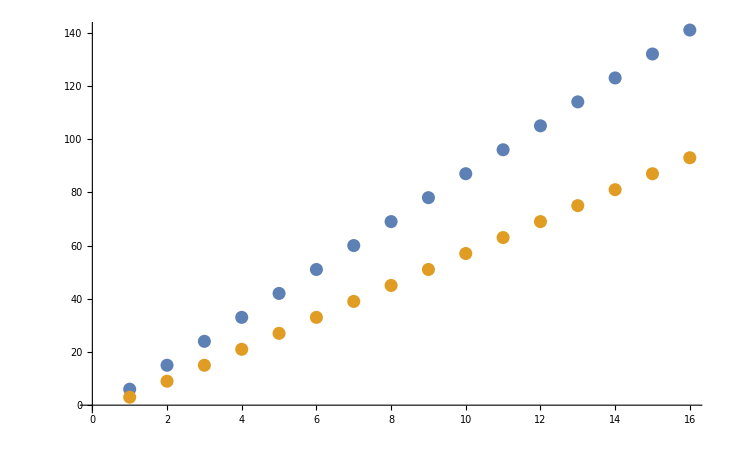

```mathematica
ListPlot[{Table[dof[3,n],{n,4,50,3}],Table[dof[3,n]-(n-1),{n,4,50,3}]}]
```

```mathematica
Collect[dof[m,n],n]
```

-1/2 m (1+m)+m n

```mathematica
Collect[Simplify[dof[m,n]-(n-1)],n]
```

-1/2 (-1+m) (2+m)+(-1+m) n

```mathematica
Collect[Simplify[dof[3,n]],n]
```

-6+3 n

```mathematica
Collect[Simplify[dof[3,n]-(n-1)],n]
```

-5+2 n

```mathematica
Table[{n,dof[3,n],dof[3,n]-(n-1)},{n,4,50,3}]//MatrixForm
```

(4 | 6 | 3
7 | 15 | 9
10 | 24 | 15
13 | 33 | 21
16 | 42 | 27
19 | 51 | 33
22 | 60 | 39
25 | 69 | 45
28 | 78 | 51
31 | 87 | 57
34 | 96 | 63
37 | 105 | 69
40 | 114 | 75
43 | 123 | 81
46 | 132 | 87
49 | 141 | 93)

```mathematica
rot[t_,i_,j_,n_]:=Module[{mm,tt},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[tt],"=",ToString[t],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Cos[tt];mm[[i,j]]=-Sin[tt];mm[[j,i]]=Sin[tt];mm[[j,j]]=Cos[tt];mm)]
```

```mathematica
rot[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[x[2,3]] | -Sin[x[2,3]] | 0
0 | Sin[x[2,3]] | Cos[x[2,3]] | 0
0 | 0 | 0 | 1)

```mathematica
rot2[x_,i_,j_,n_]:=Module[{mm,xx},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[xx],"=",ToString[x],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Sqrt[1-xx];mm[[i,j]]=-Sqrt[xx];mm[[j,i]]=Sqrt[xx];mm[[j,j]]=Sqrt[1-xx];mm)]
```

```mathematica
rot2[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | √(1-x[2,3]) | -√x[2,3] | 0
0 | √x[2,3] | √(1-x[2,3]) | 0
0 | 0 | 0 | 1)

```mathematica
fullRotMat[t_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot[t,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat[t,1,3]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Sin[t[1,2]] | -Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] | -Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | Cos[t[1,3]])

```mathematica
fullRotMat2[x_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot2[x,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat2[t,1,3]//MatrixForm
```

(√(1-t[1,2]) √(1-t[1,3]) | -√t[1,2] | -√(1-t[1,2]) √t[1,3]
√t[1,2] √(1-t[1,3]) | √(1-t[1,2]) | -√t[1,2] √t[1,3]
√t[1,3] | 0 | √(1-t[1,3]))

```mathematica
sumRows[mm_,m_,n_]:=Table[Sum[Map[Abs,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
makeEqn[ms_,n_]:=Table[Sqrt[k]==ms[[i]],{i,1,n}]
```

```mathematica
trySolve[mm_,x_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRows[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=k<=1},makeCon[x,m,n]],Reals]
)]
```

```mathematica
Table[{2,n,dof[2,n],dof[2,n]-(n-1)},{n,3,5,2}]//MatrixForm
```

(2 | 3 | 3 | 1
2 | 5 | 7 | 3)

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,5,5,3}]//MatrixForm
```

(3 | 5 | 9 | 5)

```mathematica
sumRowsNoAbs[mm_,m_,n_]:=Table[Sum[mm[[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
trySolveNoAbs[mm_,x_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRowsNoAbs[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=k<=1},makeCon[x,m,n]],Reals]
)]
```

```mathematica
makeSub[t_,x_,m_,n_]:=Flatten[Table[Table[{Sin[t[i,j]]->Sqrt[x[i,j]],Cos[t[i,j]]->Sqrt[1-x[i,j]]},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x_,m_,n_]:=Flatten[Table[Table[{0<=x[i,j]<=1},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x,2,3]
```

{0≤x[1,2]≤1,0≤x[1,3]≤1,0≤x[2,3]≤1}

```mathematica
mm=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mmzero=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mm2=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
For[n=1,n<11,n++,mm[[1,n]]=fullRotMat[t,1,n];mmzero[[1,n]]=(mm[[1,n]]/.makeSub[t,x,1,n])[[;;,1;;1]];Print[trySolveNoAbs[mmzero[[1,n]],x,1,n]]]
```

{{k→1}}

{{k→1/2,x[1,2]→1/2}}

{{k→1/3,x[1,2]→1/2,x[1,3]→1/3}}

{{k→1/4,x[1,2]→1/2,x[1,3]→1/3,x[1,4]→1/4}}

{{k→1/5,x[1,2]→1/2,x[1,3]→1/3,x[1,4]→1/4,x[1,5]→1/5}}

{{k→1/6,x[1,2]→1/2,x[1,3]→1/3,x[1,4]→1/4,x[1,5]→1/5,x[1,6]→1/6}}

{{k→1/7,x[1,2]→1/2,x[1,3]→1/3,x[1,4]→1/4,x[1,5]→1/5,x[1,6]→1/6,x[1,7]→1/7}}

{{k→1/8,x[1,2]→1/2,x[1,3]→1/3,x[1,4]→1/4,x[1,5]→1/5,x[1,6]→1/6,x[1,7]→1/7,x[1,8]→1/8}}

{{k→1/9,x[1,2]→1/2,x[1,3]→1/3,x[1,4]→1/4,x[1,5]→1/5,x[1,6]→1/6,x[1,7]→1/7,x[1,8]→1/8,x[1,9]→1/9}}

{{k→1/10,x[1,2]→1/2,x[1,3]→1/3,x[1,4]→1/4,x[1,5]→1/5,x[1,6]→1/6,x[1,7]→1/7,x[1,8]→1/8,x[1,9]→1/9,x[1,10]→1/10}}

```mathematica
MatrixForm[Table[MatrixForm[mmzero[[1,n]]],{n,2,10}]]
```

((√(1-x[1,2])
√x[1,2])
(√(1-x[1,2]) √(1-x[1,3])
√x[1,2] √(1-x[1,3])
√x[1,3])
(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4])
√x[1,2] √(1-x[1,3]) √(1-x[1,4])
√x[1,3] √(1-x[1,4])
√x[1,4])
(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5])
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5])
√x[1,3] √(1-x[1,4]) √(1-x[1,5])
√x[1,4] √(1-x[1,5])
√x[1,5])
(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6])
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6])
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6])
√x[1,4] √(1-x[1,5]) √(1-x[1,6])
√x[1,5] √(1-x[1,6])
√x[1,6])
(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7])
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7])
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7])
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7])
√x[1,5] √(1-x[1,6]) √(1-x[1,7])
√x[1,6] √(1-x[1,7])
√x[1,7])
(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8])
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8])
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8])
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8])
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8])
√x[1,6] √(1-x[1,7]) √(1-x[1,8])
√x[1,7] √(1-x[1,8])
√x[1,8])
(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9])
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9])
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9])
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9])
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9])
√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9])
√x[1,7] √(1-x[1,8]) √(1-x[1,9])
√x[1,8] √(1-x[1,9])
√x[1,9])
(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10])
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10])
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10])
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10])
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10])
√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10])
√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10])
√x[1,8] √(1-x[1,9]) √(1-x[1,10])
√x[1,9] √(1-x[1,10])
√x[1,10]))

```mathematica
mm[[2,3]]=fullRotMat[t,2,3];
```

```mathematica
mmzero[[2,3]]=FullSimplify[(((mm[[2,3]][[;;,1;;2]])/.makeSub[t,x,2,3])/.{x[1,3]->0})/.{},Assumptions->{0<=k<=1,Reals}];mmzero[[2,3]]//MatrixForm
```

(√(1-x[1,2]) | -√x[1,2] √(1-x[2,3])
√x[1,2] | √(1-x[1,2]) √(1-x[2,3])
0 | √x[2,3])

```mathematica
mmzero00200301=FullSimplify[(((mm[[2,3]][[;;,1;;2]])/.makeSub[t,x,2,3])/.{x[1,3]->0})/.{x[2,3]->k},Assumptions->{0<=k<=1,Reals}];mmzero00200301//MatrixForm
```

(√(1-x[1,2]) | -√(-((-1+k) x[1,2]))
√x[1,2] | √((-1+k) (-1+x[1,2]))
0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00200301[[2,1]]+mmzero00200301[[2,2]]==mmzero00200301[[3,2]],0<=k<=1,-1<x[1,2]<0|| 0<x[1,2]<1},x[1,2],Assumptions->{0<=k<=1,Reals}],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,2]→ConditionalExpression[(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2, k>1/2]}}

```mathematica
mmzero00200302=FullSimplify[(((mm[[2,3]][[;;,1;;2]])/.makeSub[t,x,2,3])/.{x[1,3]->0})/.{x[2,3]->k,x[1,2]->(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2},Assumptions->{0<=k<=1,Reals}];mmzero00200302//MatrixForm
```

(√(-((-1+k) (2+2 √2 √k+k))/(-2+k)^2) | -√(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2))/(-2+k)^2)
√((2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2) | √(((-1+k)^2 (2+2 √2 √k+k))/(-2+k)^2)
0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00200302[[1,1]]-mmzero00200302[[1,2]]==mmzero00200302[[3,2]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→8/9}}

```mathematica
mm[[2,4]]=fullRotMat[t,2,4];
```

```mathematica
mmzero[[2,4]]=FullSimplify[(((mm[[2,4]][[;;,1;;2]])/.makeSub[t,x,2,4])/.{x[1,4]->0,x[2,3]->0,x[1,2]->0})/.{},Assumptions->{0<=k<=1,Reals}];mmzero[[2,4]]//MatrixForm
```

(√(1-x[1,3]) | 0
0 | √(1-x[2,4])
√x[1,3] | 0
0 | √x[2,4])

```mathematica
mmzero00200401=FullSimplify[(((mm[[2,4]][[;;,1;;2]])/.makeSub[t,x,2,4])/.{x[1,4]->0,x[2,3]->0,x[1,2]->0})/.{x[2,4]->k,x[1,3]->k},Assumptions->{0<=k<=1,Reals}];mmzero00200401//MatrixForm
```

(√(1-k) | 0
0 | √(1-k)
√k | 0
0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00200401[[2,2]]==mmzero00200401[[4,2]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→1/2}}

```mathematica
mm[[2,5]]=fullRotMat[t,2,5];
```

```mathematica
mmzero[[2,5]]=FullSimplify[(((mm[[2,5]][[;;,1;;2]])/.makeSub[t,x,2,5])/.{x[1,5]->0,x[2,4]->0,x[1,3]->0})/.{},Assumptions->{0<=k<=1,Reals}];mmzero[[2,5]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,4]) | -√x[1,2] √(1-x[2,3]) √(1-x[2,5])
√x[1,2] √(1-x[1,4]) | √(1-x[1,2]) √(1-x[2,3]) √(1-x[2,5])
0 | √x[2,3] √(1-x[2,5])
√x[1,4] | 0
0 | √x[2,5])

```mathematica
mmzero00200501=FullSimplify[(((mm[[2,5]][[;;,1;;2]])/.makeSub[t,x,2,5])/.{x[1,5]->0,x[2,4]->0,x[1,3]->0})/.{x[2,5]->k,x[1,4]->k},Assumptions->{1<=l<Infinity,Reals}];mmzero00200501//MatrixForm
```

(√(1-k) √(1-x[1,2]) | -√(1-k) √x[1,2] √(1-x[2,3])
√(1-k) √x[1,2] | √(1-k) √(1-x[1,2]) √(1-x[2,3])
0 | √(1-k) √x[2,3]
√k | 0
0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00200501[[3,2]]==mmzero00200501[[5,2]],0<=k<=1},x[2,3],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[2,3]→ConditionalExpression[-k/(-1+k), 0<k<1]}}

```mathematica
mmzero00200502=FullSimplify[(((mm[[2,5]][[;;,1;;2]])/.makeSub[t,x,2,5])/.{x[1,5]->0,x[2,4]->0,x[1,3]->0})/.{x[2,5]->k,x[1,4]->k,x[2,3]->-k/(-1+k)},Assumptions->{0<=k<=1,Reals}];mmzero00200502//MatrixForm
```

(√((-1+k) (-1+x[1,2])) | -√(1-2 k) √x[1,2]
√(-((-1+k) x[1,2])) | √(1-2 k) √(1-x[1,2])
0 | √k
√k | 0
0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00200502[[2,1]]+mmzero00200502[[2,2]]==mmzero00200502[[5,2]],0<=k<=1},x[1,2],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,2]→ConditionalExpression[(2-7 k+7 k^2+2 √2 √(-((-1+k) k)) (-1+2 k))/(2-3 k)^2, 1/3<k<1/2]}}

```mathematica
mmzero00200503=FullSimplify[(((mm[[2,5]][[;;,1;;2]])/.makeSub[t,x,2,5])/.{x[1,5]->0,x[2,4]->0,x[1,3]->0})/.{x[2,5]->k,x[1,4]->k,x[2,3]->-k/(-1+k),x[1,2]->(2-7 k+7 k^2+2 √2 √(-((-1+k) k)) (-1+2 k))/(2-3 k)^2},Assumptions->{1<=l<Infinity,Reals}];mmzero00200503//MatrixForm
```

(√(1-k) √(((-1+2 k) (-2+k-2 √2 √(-((-1+k) k))))/(2-3 k)^2) | -√(1-2 k) √((2-7 k+7 k^2+2 √2 √(-((-1+k) k)) (-1+2 k))/(2-3 k)^2)
√(1-k) √((2-7 k+7 k^2+2 √2 √(-((-1+k) k)) (-1+2 k))/(2-3 k)^2) | √(1-2 k) √(((-1+2 k) (-2+k-2 √2 √(-((-1+k) k))))/(2-3 k)^2)
0 | √(1-k) √(-k/(-1+k))
√k | 0
0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00200503[[1,1]]-mmzero00200503[[1,2]]==mmzero00200503[[5,2]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→8/17}}

```mathematica
FullSimplify[(n/2-3/8)/.{n->2j+1}]
```

41/8

```mathematica
FullSimplify[(k-n/2+3/8)/.{n->2j+1}]
```

-41/8+k

```mathematica
MatrixForm[Table[MatrixForm[mmzero[[2,n]]],{n,3,10}]]
```

((√(1-x[1,2]) | -√x[1,2] √(1-x[2,3])
√x[1,2] | √(1-x[1,2]) √(1-x[2,3])
0 | √x[2,3])
(√(1-x[1,3]) | 0
0 | √(1-x[2,4])
√x[1,3] | 0
0 | √x[2,4])
(√(1-x[1,2]) √(1-x[1,4]) | -√x[1,2] √(1-x[2,3]) √(1-x[2,5])
√x[1,2] √(1-x[1,4]) | √(1-x[1,2]) √(1-x[2,3]) √(1-x[2,5])
0 | √x[2,3] √(1-x[2,5])
√x[1,4] | 0
0 | √x[2,5])
0
0
0
0
0)

```mathematica
mm[[3,4]]=fullRotMat[t,3,4];
```

```mathematica
Timing[mmtemp=FullSimplify[(((mm[[3,4]][[;;,1;;3]])/.makeSub[t,x,3,4])/.{})/.{},Assumptions->{0<=k<=1,Reals}]][[1]]
mmtemp//MatrixForm
```

0.840279

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) | -√(1-x[1,2]) (√x[1,3] √x[2,3] √(1-x[2,4])+√(1-x[1,3]) √x[1,4] √x[2,4])-√x[1,2] √(1-x[2,3]) √(1-x[2,4]) | (-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(√(1-x[1,2]) (-√(1-x[1,3]) √x[1,4] √(1-x[2,4])+√x[1,3] √x[2,3] √x[2,4])+√x[1,2] √(1-x[2,3]) √x[2,4]) √x[3,4]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) | (√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4] | -√x[1,2] (√x[1,3] (√(1-x[2,3]) √(1-x[3,4])-√x[2,3] √x[2,4] √x[3,4])+√(1-x[1,3]) √x[1,4] √(1-x[2,4]) √x[3,4])-√(1-x[1,2]) (√x[2,3] √(1-x[3,4])+√(1-x[2,3]) √x[2,4] √x[3,4])
√x[1,3] √(1-x[1,4]) | √(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4] | √(1-x[1,3]) (√(1-x[2,3]) √(1-x[3,4])-√x[2,3] √x[2,4] √x[3,4])-√x[1,3] √x[1,4] √(1-x[2,4]) √x[3,4]
√x[1,4] | √(1-x[1,4]) √x[2,4] | √(1-x[1,4]) √(1-x[2,4]) √x[3,4])

```mathematica
mmzero[[3,4]]=mmtemp/.{x[1,4]->0,x[2,4]->0,x[1,3]->0};mmzero[[3,4]]//MatrixForm
```

(√(1-x[1,2]) | -√x[1,2] √(1-x[2,3]) | √x[1,2] √x[2,3] √(1-x[3,4])
√x[1,2] | √(1-x[1,2]) √(1-x[2,3]) | -√(1-x[1,2]) √x[2,3] √(1-x[3,4])
0 | √x[2,3] | √(1-x[2,3]) √(1-x[3,4])
0 | 0 | √x[3,4])

```mathematica
mmzero00300401=FullSimplify[(mmzero[[3,4]])/.{x[3,4]->k},Assumptions->{0<=k<=1,Reals}];mmzero00300401//MatrixForm
```

(√(1-x[1,2]) | -√x[1,2] √(1-x[2,3]) | √(-((-1+k) x[1,2])) √x[2,3]
√x[1,2] | √(1-x[1,2]) √(1-x[2,3]) | -√((-1+k) (-1+x[1,2])) √x[2,3]
0 | √x[2,3] | √((-1+k) (-1+x[2,3]))
0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00300401[[3,2]]+mmzero00300401[[3,3]]==mmzero00300401[[4,3]],0<=k<=1},x[2,3],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[2,3]→ConditionalExpression[(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2, 1/2<k<1]}}

```mathematica
mmzero00300402=FullSimplify[(mmzero[[3,4]])/.{x[3,4]->k,x[2,3]->(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2},Assumptions->{0<=k<=1,Reals}];mmzero00300402//MatrixForm
```

(√(1-x[1,2]) | -√(-((-1+k) (2+2 √2 √k+k) x[1,2])/(-2+k)^2) | √(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) x[1,2])/(-2+k)^2)
√x[1,2] | √(((-1+k) (2+2 √2 √k+k) (-1+x[1,2]))/(-2+k)^2) | -√(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) (1-x[1,2]))/(-2+k)^2)
0 | √((2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2) | √(((-1+k)^2 (2+2 √2 √k+k))/(-2+k)^2)
0 | 0 | √k)

```mathematica
mmzero00300403=FullSimplify[(mmzero[[3,4]])/.{x[3,4]->k,x[2,3]->(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2,x[1,2]->1/2},Assumptions->{0<=k<=1,Reals}];mmzero00300403//MatrixForm
```

(1/(√2) | -(√(-((-1+k) (2+2 √2 √k+k))/(-2+k)^2))/(√2) | (√(1-k) Abs[-2+√2 √k+2 k])/(4-2 k)
1/(√2) | (√(-((-1+k) (2+2 √2 √k+k))/(-2+k)^2))/(√2) | (√(1-k) Abs[-2+√2 √k+2 k])/(2 (-2+k))
0 | √((2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2) | √(((-1+k)^2 (2+2 √2 √k+k))/(-2+k)^2)
0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00300403[[1,1]]-mmzero00300403[[1,2]]+mmzero00300403[[1,3]]==mmzero00300403[[4,3]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→Root0.985Root[4-28 #1-7 #1^2+16 #1^3+16 #1^4&,2]0.9852946843601814}}

```mathematica
N[mmzero00300403/.{k->Root"0.985"Root[4-28 #1-7 #1^2+16 #1^3+16 #1^4&,2]0.9852946843601814}]//MatrixForm
```

(0.707107 | -0.203389 | 0.0821239
0.707107 | 0.203389 | -0.0821239
0. | 0.95774 | 0.0348803
0. | 0. | 0.99262)

```mathematica
FullSimplify[(1/Sqrt[k])/.{k->Root"0.985"Root[4-28 #1-7 #1^2+16 #1^3+16 #1^4&,2]0.9852946843601814}]
```

Root1.01Root[16+16 #1^2-7 #1^4-28 #1^6+4 #1^8&,3]1.0074347568842794

```mathematica
N[FullSimplify[(1/Sqrt[k])/.{k->Root"0.985"Root[4-28 #1-7 #1^2+16 #1^3+16 #1^4&,2]0.9852946843601814}],20]
```

1.0074347568842793761

```mathematica
mm[[3,7]]=fullRotMat[t,3,7];
```

```mathematica
mm2[[3,7]]=fullRotMat2[x,3,7]; mm2[[3,7]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | ((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | ((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | (-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | ((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | ((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | (-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | (((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | (((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | (-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4] | (-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | ((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | ((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | √(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) | (-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5] | (-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) | (√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7] | (√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | 0 | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) | (-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6] | (-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]
√x[1,6] √(1-x[1,7]) | √(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7] | √(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7] | 0 | 0 | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) | (-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]
√x[1,7] | √(1-x[1,7]) √x[2,7] | √(1-x[1,7]) √(1-x[2,7]) √x[3,7] | 0 | 0 | 0 | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]))

```mathematica
mmzero[[3,7]]=mm2[[3,7]][[;;,1;;3]]/.{x[3,7]->0,x[3,6]->0,x[3,5]->0,x[3,4]->0,x[2,7]->0,x[2,6]->0,x[2,3]->0,x[1,5]->0,x[1,4]->0};mmzero[[3,7]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,6]) √(1-x[1,7]) | -√x[1,2] √(1-x[2,4]) √(1-x[2,5]) | -√(1-x[1,2]) √x[1,3]
√x[1,2] √(1-x[1,3]) √(1-x[1,6]) √(1-x[1,7]) | √(1-x[1,2]) √(1-x[2,4]) √(1-x[2,5]) | -√x[1,2] √x[1,3]
√x[1,3] √(1-x[1,6]) √(1-x[1,7]) | 0 | √(1-x[1,3])
0 | √x[2,4] √(1-x[2,5]) | 0
0 | √x[2,5] | 0
√x[1,6] √(1-x[1,7]) | 0 | 0
√x[1,7] | 0 | 0)

```mathematica
mmzero00300701=FullSimplify[(mmzero[[3,7]])/.{x[1,7]->k,x[2,5]->k},Assumptions->{0<=k<=1,Reals}];mmzero00300701//MatrixForm
```

(√((-1+k) (-1+x[1,2])) √(1-x[1,3]) √(1-x[1,6]) | -√(-((-1+k) x[1,2])) √(1-x[2,4]) | -√(1-x[1,2]) √x[1,3] | √x[1,2] √x[2,4] | √(k x[1,2]) √(1-x[2,4]) | -√(1-x[1,2]) √(1-x[1,3]) √x[1,6] | -√(k-k x[1,2]) √(1-x[1,3]) √(1-x[1,6])
√(-((-1+k) x[1,2])) √(1-x[1,3]) √(1-x[1,6]) | √((-1+k) (-1+x[1,2])) √(1-x[2,4]) | -√x[1,2] √x[1,3] | -√(1-x[1,2]) √x[2,4] | -√(k-k x[1,2]) √(1-x[2,4]) | -√x[1,2] √(1-x[1,3]) √x[1,6] | -√(k x[1,2]) √(1-x[1,3]) √(1-x[1,6])
√(-((-1+k) x[1,3])) √(1-x[1,6]) | 0 | √(1-x[1,3]) | 0 | 0 | -√x[1,3] √x[1,6] | -√(k x[1,3]) √(1-x[1,6])
0 | √(-((-1+k) x[2,4])) | 0 | √(1-x[2,4]) | -√(k x[2,4]) | 0 | 0
0 | √k | 0 | 0 | √(1-k) | 0 | 0
√(-((-1+k) x[1,6])) | 0 | 0 | 0 | 0 | √(1-x[1,6]) | -√(k x[1,6])
√k | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00300701[[6,1]]==mmzero00300701[[7,1]],0<=k<=1},x[1,6],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,6]→ConditionalExpression[-k/(-1+k), 0<k<1]}}

```mathematica
mmzero00300702=FullSimplify[(mmzero[[3,7]])/.{x[1,7]->k,x[2,5]->k,x[1,6]->-k/(k-1),x[2,4]->k/(1-k)},Assumptions->{0<=k<=1,Reals}];mmzero00300702//MatrixForm
```

(√(1-2 k) √(1-x[1,2]) √(1-x[1,3]) | -√(1-2 k) √x[1,2] | -√(1-x[1,2]) √x[1,3] | √(-(k x[1,2])/(-1+k)) | √(1+1/(-1+k)+2 k) √x[1,2] | -√((k (-1+x[1,2]))/(-1+k)) √(1-x[1,3]) | -√(1+1/(-1+k)+2 k) √(1-x[1,2]) √(1-x[1,3])
√(1-2 k) √x[1,2] √(1-x[1,3]) | √(1-2 k) √(1-x[1,2]) | -√x[1,2] √x[1,3] | -√((k (-1+x[1,2]))/(-1+k)) | -√(1+1/(-1+k)+2 k) √(1-x[1,2]) | -√(-(k x[1,2])/(-1+k)) √(1-x[1,3]) | -√(1+1/(-1+k)+2 k) √x[1,2] √(1-x[1,3])
√(1-2 k) √x[1,3] | 0 | √(1-x[1,3]) | 0 | 0 | -√(-(k x[1,3])/(-1+k)) | -√(1+1/(-1+k)+2 k) √x[1,3]
0 | √k | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0
0 | √k | 0 | 0 | √(1-k) | 0 | 0
√k | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00300702[[3,1]]+mmzero00300702[[3,3]]==mmzero00300702[[7,1]],0<=k<=1},x[1,3],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,3]→ConditionalExpression[(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2), 1/3<k<1/2]}}

```mathematica
mmzero00300703=FullSimplify[(mmzero[[3,7]])/.{x[1,7]->k,x[2,5]->k,x[1,6]->-k/(k-1),x[2,4]->k/(1-k),x[1,3]->(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2)},Assumptions->{0<=k<=1,Reals}];mmzero00300703//MatrixForm
```

(√(1/2-k) √((1+3 (-1+k) k-√(k (2+k (-7+6 k))))/(-1+k)^2) √(1-x[1,2]) | -√(1-2 k) √x[1,2] | -(√((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2) √(1-x[1,2]))/(√2) | √(-(k x[1,2])/(-1+k)) | √(1+1/(-1+k)+2 k) √x[1,2] | -(√((k (-1-3 (-1+k) k+√(k (2+k (-7+6 k)))))/(-1+k)^3) √(1-x[1,2]))/(√2) | -√(1+1/(-1+k)+2 k) √(1-(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2)) √(1-x[1,2])
√(1/2-k) √((1+3 (-1+k) k-√(k (2+k (-7+6 k))))/(-1+k)^2) √x[1,2] | √(1-2 k) √(1-x[1,2]) | -(√((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2) √x[1,2])/(√2) | -√((k (-1+x[1,2]))/(-1+k)) | -√(1+1/(-1+k)+2 k) √(1-x[1,2]) | -(√((k (-1-3 (-1+k) k+√(k (2+k (-7+6 k)))))/(-1+k)^3) √x[1,2])/(√2) | -√(1+1/(-1+k)+2 k) √(1-(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2)) √x[1,2]
√(1/2-k) √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2) | 0 | √(1-(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2)) | 0 | 0 | -(√((k (-1+k+k^2-√(k (2+k (-7+6 k)))))/(-1+k)^3))/(√2) | -(√(1+1/(-1+k)+2 k) √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2))/(√2)
0 | √k | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0
0 | √k | 0 | 0 | √(1-k) | 0 | 0
√k | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
(mmzero00300703/.{k->1/(1.42487766787031545744257312546820914145`19.522878745280337^2),x[1,2]->1/2})//MatrixForm
```

(0.052201638111733992 | -0.08634939773945893 | -0.56326359887084871 | 0.6966395598040682533 | 0.085071177410605624 | -0.42114626328877867 | -0.051428903190812006
0.052201638111733992 | 0.08634939773945893 | -0.56326359887084871 | -0.6966395598040682533 | -0.085071177410605624 | -0.42114626328877867 | -0.051428903190812006
0.097274945062115931 | 0 | 0.6045396896599257 | 0 | 0 | -0.78478341114208664 | -0.095834995096956345
0 | 0.7018146347220416327 | 0 | 0.17142534069380764 | -0.6914257523826974524 | 0 | 0
0 | 0.7018146347220416327 | 0 | 0 | 0.712359613180005647 | 0 | 0
0.7018146347220416327 | 0 | 0 | 0 | 0 | 0.17142534069380764 | -0.6914257523826974524
0.7018146347220416327 | 0 | 0 | 0 | 0 | 0 | 0.712359613180005647)

```mathematica
mmzero00300704=FullSimplify[(mmzero[[3,7]])/.{x[1,7]->k,x[2,5]->k,x[1,6]->-k/(k-1),x[2,4]->k/(1-k),x[1,3]->(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2),x[1,2]->1/2},Assumptions->{0<=k<=1,Reals}];mmzero00300704//MatrixForm
```

(1/2 √(1-2 k) √((1+3 (-1+k) k-√(k (2+k (-7+6 k))))/(-1+k)^2) | -√(1/2-k) | -1/2 √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2) | 1/(√(-2+2/k)) | √(k+k/(2 (-1+k))) | -1/2 √((k (-1-3 (-1+k) k+√(k (2+k (-7+6 k)))))/(-1+k)^3) | -1/2 √(1+1/(-1+k)+2 k) √((1+3 (-1+k) k-√(k (2+k (-7+6 k))))/(-1+k)^2)
1/2 √(1-2 k) √((1+3 (-1+k) k-√(k (2+k (-7+6 k))))/(-1+k)^2) | √(1/2-k) | -1/2 √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2) | -1/(√(-2+2/k)) | -√(k+k/(2 (-1+k))) | -1/2 √((k (-1-3 (-1+k) k+√(k (2+k (-7+6 k)))))/(-1+k)^3) | -1/2 √(1+1/(-1+k)+2 k) √((1+3 (-1+k) k-√(k (2+k (-7+6 k))))/(-1+k)^2)
√(1/2-k) √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2) | 0 | √(1-(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2)) | 0 | 0 | -(√((k (-1+k+k^2-√(k (2+k (-7+6 k)))))/(-1+k)^3))/(√2) | -(√(1+1/(-1+k)+2 k) √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2))/(√2)
0 | √k | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0
0 | √k | 0 | 0 | √(1-k) | 0 | 0
√k | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00300704[[2,1]]+mmzero00300704[[2,2]]-mmzero00300704[[2,3]]==mmzero00300704[[7,1]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→(Root0.702Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416)^2}}

```mathematica
N[mmzero00300704/.{k->(Root"0.702"Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416)^2}]//MatrixForm
```

(0.0522016 | -0.0863494 | -0.563264 | 0.69664 | 0.0850712 | -0.421146 | -0.0514289
0.0522016 | 0.0863494 | -0.563264 | -0.69664 | -0.0850712 | -0.421146 | -0.0514289
0.0972749 | 0. | 0.60454 | 0. | 0. | -0.784783 | -0.095835
0. | 0.701815 | 0. | 0.171425 | -0.691426 | 0. | 0.
0. | 0.701815 | 0. | 0. | 0.71236 | 0. | 0.
0.701815 | 0. | 0. | 0. | 0. | 0.171425 | -0.691426
0.701815 | 0. | 0. | 0. | 0. | 0. | 0.71236)

```mathematica
FullSimplify[(1/Sqrt[k])/.{k->(Root"0.702"Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416)^2}]
```

Root1.42Root[25-8 #1-8 #1^2+36 #1^3+2 #1^4-24 #1^5-4 #1^6+4 #1^7+#1^8&,3]1.4248776678703154

```mathematica
N[FullSimplify[(1/Sqrt[k])/.{k->(Root"0.702"Root[1+4 #1-4 #1^2-24 #1^3+2 #1^4+36 #1^5-8 #1^6-8 #1^7+25 #1^8&,4]0.7018146347220416)^2}],20]
```

1.4248776678703154575

```mathematica
mm[[3,10]]=fullRotMat[t,3,10];
```

```mathematica
mm2[[3,10]]=fullRotMat2[x,3,10];mm2[[3,10]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | (((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10] | (((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | (-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | (((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10] | (((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | (-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | ((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10] | ((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | (-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4] | (-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | (((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10] | (((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | √(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) | (-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5] | (-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | ((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10] | ((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | 0 | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) | (-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6] | (-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]
√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | (((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10] | (((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | 0 | 0 | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) | (-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7] | (-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]
√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | ((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10] | ((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | 0 | 0 | 0 | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) | (-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8] | (-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]
√x[1,8] √(1-x[1,9]) √(1-x[1,10]) | (√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10] | (√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10] | 0 | 0 | 0 | 0 | √(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) | (-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9] | (-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √x[3,10]
√x[1,9] √(1-x[1,10]) | √(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10] | √(1-x[1,9]) √(1-x[2,9]) √x[3,9] √(1-x[3,10])+(-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √x[3,10] | 0 | 0 | 0 | 0 | 0 | √(1-x[1,9]) √(1-x[2,9]) √(1-x[3,9]) | (-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √(1-x[3,10])-√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √x[3,10]
√x[1,10] | √(1-x[1,10]) √x[2,10] | √(1-x[1,10]) √(1-x[2,10]) √x[3,10] | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,10]) √(1-x[2,10]) √(1-x[3,10]))

```mathematica
mmzero[[3,10]]=mm2[[3,10]][[;;,1;;3]]/.{x[3,10]->0,x[3,9]->0,x[3,8]->0,x[3,7]->0,x[3,6]->0,x[3,5]->0,x[2,10]->0,x[2,9]->0,x[2,8]->0,x[1,7]->0,x[1,6]->0,x[1,5]->0,x[2,4]->0,x[2,3]->0,x[1,3]->1};mmzero[[3,10]]//MatrixForm
```

(0 | -√x[1,2] √(1-x[2,5]) √(1-x[2,6]) √(1-x[2,7]) | -√(1-x[1,2]) √(1-x[3,4])
0 | √(1-x[1,2]) √(1-x[2,5]) √(1-x[2,6]) √(1-x[2,7]) | -√x[1,2] √(1-x[3,4])
√(1-x[1,4]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | 0 | -√x[1,4] √x[3,4]
√x[1,4] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) | 0 | √(1-x[1,4]) √x[3,4]
0 | √x[2,5] √(1-x[2,6]) √(1-x[2,7]) | 0
0 | √x[2,6] √(1-x[2,7]) | 0
0 | √x[2,7] | 0
√x[1,8] √(1-x[1,9]) √(1-x[1,10]) | 0 | 0
√x[1,9] √(1-x[1,10]) | 0 | 0
√x[1,10] | 0 | 0)

```mathematica
mmzero00301001=FullSimplify[(mmzero[[3,10]])/.{x[1,10]->k,x[2,7]->k},Assumptions->{0<=k<=1,Reals}];mmzero00301001//MatrixForm
```

(0 | -√(-((-1+k) x[1,2])) √(1-x[2,5]) √(1-x[2,6]) | -√(1-x[1,2]) √(1-x[3,4]) | √(1-x[1,2]) √x[3,4] | √x[1,2] √x[2,5] | √x[1,2] √(1-x[2,5]) √x[2,6] | √(k x[1,2]) √(1-x[2,5]) √(1-x[2,6]) | 0 | 0 | 0
0 | √((-1+k) (-1+x[1,2])) √(1-x[2,5]) √(1-x[2,6]) | -√x[1,2] √(1-x[3,4]) | √x[1,2] √x[3,4] | -√(1-x[1,2]) √x[2,5] | -√(1-x[1,2]) √(1-x[2,5]) √x[2,6] | -√(k-k x[1,2]) √(1-x[2,5]) √(1-x[2,6]) | 0 | 0 | 0
√((-1+k) (-1+x[1,4])) √(1-x[1,8]) √(1-x[1,9]) | 0 | -√x[1,4] √x[3,4] | -√x[1,4] √(1-x[3,4]) | 0 | 0 | 0 | -√(1-x[1,4]) √x[1,8] | -√(1-x[1,4]) √(1-x[1,8]) √x[1,9] | -√(k-k x[1,4]) √(1-x[1,8]) √(1-x[1,9])
√(-((-1+k) x[1,4])) √(1-x[1,8]) √(1-x[1,9]) | 0 | √(1-x[1,4]) √x[3,4] | √(1-x[1,4]) √(1-x[3,4]) | 0 | 0 | 0 | -√x[1,4] √x[1,8] | -√x[1,4] √(1-x[1,8]) √x[1,9] | -√(k x[1,4]) √(1-x[1,8]) √(1-x[1,9])
0 | √(-((-1+k) x[2,5])) √(1-x[2,6]) | 0 | 0 | √(1-x[2,5]) | -√x[2,5] √x[2,6] | -√(k x[2,5]) √(1-x[2,6]) | 0 | 0 | 0
0 | √(-((-1+k) x[2,6])) | 0 | 0 | 0 | √(1-x[2,6]) | -√(k x[2,6]) | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0
√(-((-1+k) x[1,8])) √(1-x[1,9]) | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,8]) | -√x[1,8] √x[1,9] | -√(k x[1,8]) √(1-x[1,9])
√(-((-1+k) x[1,9])) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,9]) | -√(k x[1,9])
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00301001[[9,1]]==mmzero00301001[[10,1]],0<=k<=1},x[1,9],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,9]→ConditionalExpression[-k/(-1+k), 0<k<1]}}

```mathematica
mmzero00301002=FullSimplify[(mmzero[[3,10]])/.{x[1,10]->k,x[2,7]->k,x[1,9]->-k/(-1+k),x[2,6]->-k/(-1+k)},Assumptions->{0<=k<=1,Reals}];mmzero00301002//MatrixForm
```

(0 | -√(1-2 k) √x[1,2] √(1-x[2,5]) | -√(1-x[1,2]) √(1-x[3,4]) | √(1-x[1,2]) √x[3,4] | √x[1,2] √x[2,5] | √(-(k x[1,2])/(-1+k)) √(1-x[2,5]) | √(1+1/(-1+k)+2 k) √x[1,2] √(1-x[2,5]) | 0 | 0 | 0
0 | √(1-2 k) √(1-x[1,2]) √(1-x[2,5]) | -√x[1,2] √(1-x[3,4]) | √x[1,2] √x[3,4] | -√(1-x[1,2]) √x[2,5] | -√((k (-1+x[1,2]))/(-1+k)) √(1-x[2,5]) | -√(1+1/(-1+k)+2 k) √(1-x[1,2]) √(1-x[2,5]) | 0 | 0 | 0
√(1-2 k) √(1-x[1,4]) √(1-x[1,8]) | 0 | -√x[1,4] √x[3,4] | -√x[1,4] √(1-x[3,4]) | 0 | 0 | 0 | -√(1-x[1,4]) √x[1,8] | -√((k (-1+x[1,4]))/(-1+k)) √(1-x[1,8]) | -√(1+1/(-1+k)+2 k) √(1-x[1,4]) √(1-x[1,8])
√(1-2 k) √x[1,4] √(1-x[1,8]) | 0 | √(1-x[1,4]) √x[3,4] | √(1-x[1,4]) √(1-x[3,4]) | 0 | 0 | 0 | -√x[1,4] √x[1,8] | -√(-(k x[1,4])/(-1+k)) √(1-x[1,8]) | -√(1+1/(-1+k)+2 k) √x[1,4] √(1-x[1,8])
0 | √(1-2 k) √x[2,5] | 0 | 0 | √(1-x[2,5]) | -√(-(k x[2,5])/(-1+k)) | -√(1+1/(-1+k)+2 k) √x[2,5] | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0
√(1-2 k) √x[1,8] | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,8]) | -√(-(k x[1,8])/(-1+k)) | -√(1+1/(-1+k)+2 k) √x[1,8]
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00301002[[8,1]]==mmzero00301002[[10,1]],0<=k<=1},x[1,8],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,8]→ConditionalExpression[k/(1-2 k), 0<k<1/2]}}

```mathematica
mmzero00301003=FullSimplify[(mmzero[[3,10]])/.{x[1,10]->k,x[2,7]->k,x[1,9]->-k/(-1+k),x[2,6]->-k/(-1+k),x[1,8]->k/(1-2k),x[2,5]->k/(1-2k)},Assumptions->{0<=k<=1/2,Reals}];mmzero00301003//MatrixForm
```

(0 | -√(1-3 k) √x[1,2] | -√(1-x[1,2]) √(1-x[3,4]) | √(1-x[1,2]) √x[3,4] | √((k x[1,2])/(1-2 k)) | √((k-3 k^2)/(1-3 k+2 k^2)) √x[1,2] | √((3+2/(-1+k)) k) √x[1,2] | 0 | 0 | 0
0 | √(1-3 k) √(1-x[1,2]) | -√x[1,2] √(1-x[3,4]) | √x[1,2] √x[3,4] | -√((k (-1+x[1,2]))/(-1+2 k)) | -√((k-3 k^2)/(1-3 k+2 k^2)) √(1-x[1,2]) | -√((3+2/(-1+k)) k) √(1-x[1,2]) | 0 | 0 | 0
√(1-3 k) √(1-x[1,4]) | 0 | -√x[1,4] √x[3,4] | -√x[1,4] √(1-x[3,4]) | 0 | 0 | 0 | -√((k (-1+x[1,4]))/(-1+2 k)) | -√((k-3 k^2)/(1-3 k+2 k^2)) √(1-x[1,4]) | -√((3+2/(-1+k)) k) √(1-x[1,4])
√(1-3 k) √x[1,4] | 0 | √(1-x[1,4]) √x[3,4] | √(1-x[1,4]) √(1-x[3,4]) | 0 | 0 | 0 | -√((k x[1,4])/(1-2 k)) | -√((k-3 k^2)/(1-3 k+2 k^2)) √x[1,4] | -√((3+2/(-1+k)) k) √x[1,4]
0 | √k | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0
√k | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
mmzero00301004=FullSimplify[(mmzero[[3,10]])/.{x[1,10]->k,x[2,7]->k,x[1,9]->-k/(-1+k),x[2,6]->-k/(-1+k),x[1,8]->k/(1-2k),x[2,5]->k/(1-2k),x[1,4]->1/2,x[1,2]->1/2,x[3,4]->1/2},Assumptions->{0<=k<=1/2,Reals}];mmzero00301004//MatrixForm
```

(0 | -(√(1-3 k))/(√2) | -1/2 | 1/2 | 1/(√(-4+2/k)) | √((k-3 k^2)/(2-6 k+4 k^2)) | √(1+1/(-1+k)+(3 k)/2) | 0 | 0 | 0
0 | (√(1-3 k))/(√2) | -1/2 | 1/2 | -1/(√(-4+2/k)) | -√((k-3 k^2)/(2-6 k+4 k^2)) | -√(1+1/(-1+k)+(3 k)/2) | 0 | 0 | 0
(√(1-3 k))/(√2) | 0 | -1/2 | -1/2 | 0 | 0 | 0 | -1/(√(-4+2/k)) | -√((k-3 k^2)/(2-6 k+4 k^2)) | -√(1+1/(-1+k)+(3 k)/2)
(√(1-3 k))/(√2) | 0 | 1/2 | 1/2 | 0 | 0 | 0 | -1/(√(-4+2/k)) | -√((k-3 k^2)/(2-6 k+4 k^2)) | -√(1+1/(-1+k)+(3 k)/2)
0 | √k | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0
√k | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
({{0, -(√(1-3 k))/(√2), -1/2}, {0, (√(1-3 k))/(√2), -1/2}, {(√(1-3 k))/(√2), 0, -1/2}, {(√(1-3 k))/(√2), 0, 1/2}, {0, √k, 0}, {0, √k, 0}, {0, √k, 0}, {√k, 0, 0}, {√k, 0, 0}, {√k, 0, 0}})
```

{{0,-(√(1-3 k))/(√2),-1/2},{0,(√(1-3 k))/(√2),-1/2},{(√(1-3 k))/(√2),0,-1/2},{(√(1-3 k))/(√2),0,1/2},{0,√k,0},{0,√k,0},{0,√k,0},{√k,0,0},{√k,0,0},{√k,0,0}}

```mathematica
FullSimplify[Solve[{mmzero00301004[[4,1]]+mmzero00301004[[4,3]]==mmzero00301004[[8,1]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→1/50 (9+2 √14)}}

```mathematica
N[FullSimplify[Solve[{mmzero00301004[[4,1]]+mmzero00301004[[4,3]]==mmzero00301004[[8,1]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}],20]
```

{{k→0.32966629547095765542}}

```mathematica
FullSimplify[mmzero00301004/.{k->1/50 (9+2 √14)}]//MatrixForm
```

(0 | 1/10 (3-√14) | -1/2 | 1/2 | (√(4+√14))/4 | Root0.0891Root[1-192 #1^2+8320 #1^4&,3]0.08911068427062438 | Root0.0520Root[1-440 #1^2+26000 #1^4&,3]0.05201098424262171 | 0 | 0 | 0
0 | 1/10 (-3+√14) | -1/2 | 1/2 | -1/4 √(4+√14) | Root-0.0891Root[1-192 #1^2+8320 #1^4&,2]-0.08911068427062438 | Root-0.0520Root[1-440 #1^2+26000 #1^4&,2]-0.05201098424262171 | 0 | 0 | 0
1/10 (-3+√14) | 0 | -1/2 | -1/2 | 0 | 0 | 0 | -1/4 √(4+√14) | Root-0.0891Root[1-192 #1^2+8320 #1^4&,2]-0.08911068427062438 | Root-0.0520Root[1-440 #1^2+26000 #1^4&,2]-0.05201098424262171
1/10 (-3+√14) | 0 | 1/2 | 1/2 | 0 | 0 | 0 | -1/4 √(4+√14) | Root-0.0891Root[1-192 #1^2+8320 #1^4&,2]-0.08911068427062438 | Root-0.0520Root[1-440 #1^2+26000 #1^4&,2]-0.05201098424262171
0 | 1/10 (2+√14) | 0 | 0 | 1/2 √(2-√(7/2)) | Root-0.690Root[1-992 #1^2+2080 #1^4&,1]-0.6898643871241597 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545 | 0 | 0 | 0
0 | 1/10 (2+√14) | 0 | 0 | 0 | Root0.713Root[32-96 #1^2+65 #1^4&,3]0.712885474164995 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545 | 0 | 0 | 0
0 | 1/10 (2+√14) | 0 | 0 | 0 | 0 | 1/5 √(41/2-√14) | 0 | 0 | 0
1/10 (2+√14) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 √(2-√(7/2)) | Root-0.690Root[1-992 #1^2+2080 #1^4&,1]-0.6898643871241597 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545
1/10 (2+√14) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root0.713Root[32-96 #1^2+65 #1^4&,3]0.712885474164995 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545
1/10 (2+√14) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 √(41/2-√14))

```mathematica
N[FullSimplify[mmzero00301004/.{k->1/50 (9+2 √14)}]//MatrixForm,20]
```

(0 | -0.074165738677394138558 | -0.5 | 0.5 | 0.69559585009786489999 | 0.08911068427062437564 | 0.052010984242621712015 | 0 | 0 | 0
0 | 0.074165738677394138558 | -0.5 | 0.5 | -0.69559585009786489999 | -0.08911068427062437564 | -0.052010984242621712015 | 0 | 0 | 0
0.074165738677394138558 | 0 | -0.5 | -0.5 | 0 | 0 | 0 | -0.69559585009786489999 | -0.08911068427062437564 | -0.052010984242621712015
0.074165738677394138558 | 0 | 0.5 | 0.5 | 0 | 0 | 0 | -0.69559585009786489999 | -0.08911068427062437564 | -0.052010984242621712015
0 | 0.57416573867739413856 | 0 | 0 | 0.17970204966348415805 | -0.68986438712415966696 | -0.40265122035527544603 | 0 | 0 | 0
0 | 0.57416573867739413856 | 0 | 0 | 0 | 0.71288547416499500512 | -0.40265122035527544603 | 0 | 0 | 0
0 | 0.57416573867739413856 | 0 | 0 | 0 | 0 | 0.81873909429624914215 | 0 | 0 | 0
0.57416573867739413856 | 0 | 0 | 0 | 0 | 0 | 0 | 0.17970204966348415805 | -0.68986438712415966696 | -0.40265122035527544603
0.57416573867739413856 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.71288547416499500512 | -0.40265122035527544603
0.57416573867739413856 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.81873909429624914215)

```mathematica
FullSimplify[(1/k)/.{k->1/50 (9+2 √14)}]
```

18-4 √14

```mathematica
FullSimplify[1/Sqrt[k]/.{k->1/50 (9+2 √14)}]
```

-2+√14

```mathematica
N[FullSimplify[(1/Sqrt[k])/.{k->1/50 (9+2 √14)}],20]
```

1.7416573867739413856

```mathematica
Factor[Expand[(l-(Sqrt[14]-2))(l+(Sqrt[14]+2))]]
```

-10+4 l+l^2

```mathematica
Expand[(l-(Sqrt[14]-2))(l+(Sqrt[14]-2))(l-(Sqrt[14]+2))(l+(Sqrt[14]+2))]
```

100-36 l^2+l^4

```mathematica
Factor[Expand[(l-(Sqrt[14]-2))(l+(Sqrt[14]-2))(l-(Sqrt[14]+2))(l+(Sqrt[14]+2))]]
```

(-10-4 l+l^2) (-10+4 l+l^2)

```mathematica
mm[[3,13]]=fullRotMat[t,3,13];
```

```mathematica
mm2[[3,13]]=fullRotMat2[x,3,13];mm2[[3,13]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | (-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | (-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | (((((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | (((((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | (-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4] | (-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-((((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-(((((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((((((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | √(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) | (-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5] | (-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | (((((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | (((((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | 0 | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) | (-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6] | (-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-((((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-(((((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((((((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | 0 | 0 | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) | (-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7] | (-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8] | (-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10] | (-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | (((((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | (((((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | 0 | 0 | 0 | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) | (-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8] | (-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9] | (-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10] | (-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-((((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-(((((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((((√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | 0 | 0 | 0 | 0 | √(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) | (-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9] | (-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √x[3,10] | (-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | (((√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,9] √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | (((√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √(1-x[3,10])+(-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,9] √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,9] √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,9] √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | 0 | 0 | 0 | 0 | 0 | √(1-x[1,9]) √(1-x[2,9]) √(1-x[3,9]) | (-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √(1-x[3,10])-√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √x[3,10] | (-√x[1,9] √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √(1-x[3,10])+(-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √x[3,10]) √x[3,11] | (-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,9] √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-((√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √(1-x[3,10])+(-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,9] √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(((√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,9] √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-(((√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √(1-x[3,10])+(-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,9] √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,9] √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-((√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,9] √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,10] √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((√(1-x[1,10]) √x[2,10] √(1-x[2,11])-√x[1,10] √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,10] √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,10] √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((√(1-x[1,10]) √(1-x[2,10]) √x[3,10] √(1-x[3,11])+(-√x[1,10] √x[1,11] √(1-x[2,11])-√(1-x[1,10]) √x[2,10] √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,10] √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(√(1-x[1,10]) √x[2,10] √(1-x[2,11])-√x[1,10] √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,10] √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((√(1-x[1,10]) √x[2,10] √(1-x[2,11])-√x[1,10] √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,10] √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,10]) √(1-x[2,10]) √(1-x[3,10]) | (-√x[1,10] √x[1,11] √(1-x[2,11])-√(1-x[1,10]) √x[2,10] √x[2,11]) √(1-x[3,11])-√(1-x[1,10]) √(1-x[2,10]) √x[3,10] √x[3,11] | (-√x[1,10] √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(√(1-x[1,10]) √x[2,10] √(1-x[2,11])-√x[1,10] √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(√(1-x[1,10]) √(1-x[2,10]) √x[3,10] √(1-x[3,11])+(-√x[1,10] √x[1,11] √(1-x[2,11])-√(1-x[1,10]) √x[2,10] √x[2,11]) √x[3,11]) √x[3,12] | (-√x[1,10] √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((√(1-x[1,10]) √x[2,10] √(1-x[2,11])-√x[1,10] √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,10] √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((√(1-x[1,10]) √(1-x[2,10]) √x[3,10] √(1-x[3,11])+(-√x[1,10] √x[1,11] √(1-x[2,11])-√(1-x[1,10]) √x[2,10] √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,10] √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(√(1-x[1,10]) √x[2,10] √(1-x[2,11])-√x[1,10] √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]
√x[1,11] √(1-x[1,12]) √(1-x[1,13]) | (√(1-x[1,11]) √x[2,11] √(1-x[2,12])-√x[1,11] √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,11] √(1-x[1,12]) √x[1,13] √x[2,13] | (√(1-x[1,11]) √(1-x[2,11]) √x[3,11] √(1-x[3,12])+(-√x[1,11] √x[1,12] √(1-x[2,12])-√(1-x[1,11]) √x[2,11] √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,11] √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(√(1-x[1,11]) √x[2,11] √(1-x[2,12])-√x[1,11] √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,11]) √(1-x[2,11]) √(1-x[3,11]) | (-√x[1,11] √x[1,12] √(1-x[2,12])-√(1-x[1,11]) √x[2,11] √x[2,12]) √(1-x[3,12])-√(1-x[1,11]) √(1-x[2,11]) √x[3,11] √x[3,12] | (-√x[1,11] √(1-x[1,12]) √x[1,13] √(1-x[2,13])-(√(1-x[1,11]) √x[2,11] √(1-x[2,12])-√x[1,11] √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-(√(1-x[1,11]) √(1-x[2,11]) √x[3,11] √(1-x[3,12])+(-√x[1,11] √x[1,12] √(1-x[2,12])-√(1-x[1,11]) √x[2,11] √x[2,12]) √x[3,12]) √x[3,13]
√x[1,12] √(1-x[1,13]) | √(1-x[1,12]) √x[2,12] √(1-x[2,13])-√x[1,12] √x[1,13] √x[2,13] | √(1-x[1,12]) √(1-x[2,12]) √x[3,12] √(1-x[3,13])+(-√x[1,12] √x[1,13] √(1-x[2,13])-√(1-x[1,12]) √x[2,12] √x[2,13]) √x[3,13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,12]) √(1-x[2,12]) √(1-x[3,12]) | (-√x[1,12] √x[1,13] √(1-x[2,13])-√(1-x[1,12]) √x[2,12] √x[2,13]) √(1-x[3,13])-√(1-x[1,12]) √(1-x[2,12]) √x[3,12] √x[3,13]
√x[1,13] | √(1-x[1,13]) √x[2,13] | √(1-x[1,13]) √(1-x[2,13]) √x[3,13] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,13]) √(1-x[2,13]) √(1-x[3,13]))

```mathematica
mmzero[[3,13]]=mm2[[3,13]][[;;,1;;3]]/.{x[3,13]->0,x[3,12]->0,x[3,11]->0,x[3,10]->0,x[3,9]->0,x[3,8]->0,x[3,7]->0,x[3,6]->0,x[2,13]->0,x[2,12]->0,x[2,11]->0,x[2,10]->0,x[1,9]->0,x[1,8]->0,x[1,7]->0,x[1,6]->0,x[2,5]->0,x[1,5]->0,x[2,4]->0,x[2,3]->0,x[1,3]->1};mmzero[[3,13]]//MatrixForm
```

(0 | -√x[1,2] √(1-x[2,6]) √(1-x[2,7]) √(1-x[2,8]) √(1-x[2,9]) | -√(1-x[1,2]) √(1-x[3,4]) √(1-x[3,5])
0 | √(1-x[1,2]) √(1-x[2,6]) √(1-x[2,7]) √(1-x[2,8]) √(1-x[2,9]) | -√x[1,2] √(1-x[3,4]) √(1-x[3,5])
√(1-x[1,4]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | 0 | -√x[1,4] √x[3,4] √(1-x[3,5])
√x[1,4] √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | 0 | √(1-x[1,4]) √x[3,4] √(1-x[3,5])
0 | 0 | √x[3,5]
0 | √x[2,6] √(1-x[2,7]) √(1-x[2,8]) √(1-x[2,9]) | 0
0 | √x[2,7] √(1-x[2,8]) √(1-x[2,9]) | 0
0 | √x[2,8] √(1-x[2,9]) | 0
0 | √x[2,9] | 0
√x[1,10] √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | 0 | 0
√x[1,11] √(1-x[1,12]) √(1-x[1,13]) | 0 | 0
√x[1,12] √(1-x[1,13]) | 0 | 0
√x[1,13] | 0 | 0)

```mathematica
mmzero00301301=FullSimplify[(mmzero[[3,13]])/.{x[1,13]->k,x[2,9]->k,x[3,5]->k},Assumptions->{0<=k<=1,Reals}];mmzero00301301//MatrixForm
```

(0 | -√(-((-1+k) x[1,2])) √(1-x[2,6]) √(1-x[2,7]) √(1-x[2,8]) | -√((-1+k) (-1+x[1,2])) √(1-x[3,4]) | √(1-x[1,2]) √x[3,4] | √(k-k x[1,2]) √(1-x[3,4]) | √x[1,2] √x[2,6] | √x[1,2] √(1-x[2,6]) √x[2,7] | √x[1,2] √(1-x[2,6]) √(1-x[2,7]) √x[2,8] | √(k x[1,2]) √(1-x[2,6]) √(1-x[2,7]) √(1-x[2,8]) | 0 | 0 | 0 | 0
0 | √((-1+k) (-1+x[1,2])) √(1-x[2,6]) √(1-x[2,7]) √(1-x[2,8]) | -√(-((-1+k) x[1,2])) √(1-x[3,4]) | √x[1,2] √x[3,4] | √(k x[1,2]) √(1-x[3,4]) | -√(1-x[1,2]) √x[2,6] | -√(1-x[1,2]) √(1-x[2,6]) √x[2,7] | -√(1-x[1,2]) √(1-x[2,6]) √(1-x[2,7]) √x[2,8] | -√(k-k x[1,2]) √(1-x[2,6]) √(1-x[2,7]) √(1-x[2,8]) | 0 | 0 | 0 | 0
√((-1+k) (-1+x[1,4])) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) | 0 | -√(-((-1+k) x[1,4])) √x[3,4] | -√x[1,4] √(1-x[3,4]) | √(k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√(1-x[1,4]) √x[1,10] | -√(1-x[1,4]) √(1-x[1,10]) √x[1,11] | -√(1-x[1,4]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] | -√(k-k x[1,4]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12])
√(-((-1+k) x[1,4])) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) | 0 | √((-1+k) (-1+x[1,4])) √x[3,4] | √(1-x[1,4]) √(1-x[3,4]) | -√(k-k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√x[1,4] √x[1,10] | -√x[1,4] √(1-x[1,10]) √x[1,11] | -√x[1,4] √(1-x[1,10]) √(1-x[1,11]) √x[1,12] | -√(k x[1,4]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12])
0 | 0 | √k | 0 | √(1-k) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √(-((-1+k) x[2,6])) √(1-x[2,7]) √(1-x[2,8]) | 0 | 0 | 0 | √(1-x[2,6]) | -√x[2,6] √x[2,7] | -√x[2,6] √(1-x[2,7]) √x[2,8] | -√(k x[2,6]) √(1-x[2,7]) √(1-x[2,8]) | 0 | 0 | 0 | 0
0 | √(-((-1+k) x[2,7])) √(1-x[2,8]) | 0 | 0 | 0 | 0 | √(1-x[2,7]) | -√x[2,7] √x[2,8] | -√(k x[2,7]) √(1-x[2,8]) | 0 | 0 | 0 | 0
0 | √(-((-1+k) x[2,8])) | 0 | 0 | 0 | 0 | 0 | √(1-x[2,8]) | -√(k x[2,8]) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0 | 0
√(-((-1+k) x[1,10])) √(1-x[1,11]) √(1-x[1,12]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,10]) | -√x[1,10] √x[1,11] | -√x[1,10] √(1-x[1,11]) √x[1,12] | -√(k x[1,10]) √(1-x[1,11]) √(1-x[1,12])
√(-((-1+k) x[1,11])) √(1-x[1,12]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,11]) | -√x[1,11] √x[1,12] | -√(k x[1,11]) √(1-x[1,12])
√(-((-1+k) x[1,12])) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,12]) | -√(k x[1,12])
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00301301[[12,1]]==mmzero00301301[[13,1]],0<=k<=1},x[1,12],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,12]→ConditionalExpression[-k/(-1+k), 0<k<1]}}

```mathematica
mmzero00301302=FullSimplify[(mmzero[[3,13]])/.{x[1,13]->k,x[2,9]->k,x[3,5]->k,x[1,12]->k/(1-k),x[2,8]->k/(1-k)},Assumptions->{0<=k<=1,Reals}];mmzero00301302//MatrixForm
```

(0 | -√(1-2 k) √x[1,2] √(1-x[2,6]) √(1-x[2,7]) | -√((-1+k) (-1+x[1,2])) √(1-x[3,4]) | √(1-x[1,2]) √x[3,4] | √(k-k x[1,2]) √(1-x[3,4]) | √x[1,2] √x[2,6] | √x[1,2] √(1-x[2,6]) √x[2,7] | √(-(k x[1,2])/(-1+k)) √(1-x[2,6]) √(1-x[2,7]) | √(1+1/(-1+k)+2 k) √x[1,2] √(1-x[2,6]) √(1-x[2,7]) | 0 | 0 | 0 | 0
0 | √(1-2 k) √(1-x[1,2]) √(1-x[2,6]) √(1-x[2,7]) | -√(-((-1+k) x[1,2])) √(1-x[3,4]) | √x[1,2] √x[3,4] | √(k x[1,2]) √(1-x[3,4]) | -√(1-x[1,2]) √x[2,6] | -√(1-x[1,2]) √(1-x[2,6]) √x[2,7] | -√((k (-1+x[1,2]))/(-1+k)) √(1-x[2,6]) √(1-x[2,7]) | -√(1+1/(-1+k)+2 k) √(1-x[1,2]) √(1-x[2,6]) √(1-x[2,7]) | 0 | 0 | 0 | 0
√(1-2 k) √(1-x[1,4]) √(1-x[1,10]) √(1-x[1,11]) | 0 | -√(-((-1+k) x[1,4])) √x[3,4] | -√x[1,4] √(1-x[3,4]) | √(k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√(1-x[1,4]) √x[1,10] | -√(1-x[1,4]) √(1-x[1,10]) √x[1,11] | -√((k (-1+x[1,4]))/(-1+k)) √(1-x[1,10]) √(1-x[1,11]) | -√(1+1/(-1+k)+2 k) √(1-x[1,4]) √(1-x[1,10]) √(1-x[1,11])
√(1-2 k) √x[1,4] √(1-x[1,10]) √(1-x[1,11]) | 0 | √((-1+k) (-1+x[1,4])) √x[3,4] | √(1-x[1,4]) √(1-x[3,4]) | -√(k-k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√x[1,4] √x[1,10] | -√x[1,4] √(1-x[1,10]) √x[1,11] | -√(-(k x[1,4])/(-1+k)) √(1-x[1,10]) √(1-x[1,11]) | -√(1+1/(-1+k)+2 k) √x[1,4] √(1-x[1,10]) √(1-x[1,11])
0 | 0 | √k | 0 | √(1-k) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √(1-2 k) √x[2,6] √(1-x[2,7]) | 0 | 0 | 0 | √(1-x[2,6]) | -√x[2,6] √x[2,7] | -√(-(k x[2,6])/(-1+k)) √(1-x[2,7]) | -√(1+1/(-1+k)+2 k) √x[2,6] √(1-x[2,7]) | 0 | 0 | 0 | 0
0 | √(1-2 k) √x[2,7] | 0 | 0 | 0 | 0 | √(1-x[2,7]) | -√(-(k x[2,7])/(-1+k)) | -√(1+1/(-1+k)+2 k) √x[2,7] | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0 | 0
√(1-2 k) √x[1,10] √(1-x[1,11]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,10]) | -√x[1,10] √x[1,11] | -√(-(k x[1,10])/(-1+k)) √(1-x[1,11]) | -√(1+1/(-1+k)+2 k) √x[1,10] √(1-x[1,11])
√(1-2 k) √x[1,11] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,11]) | -√(-(k x[1,11])/(-1+k)) | -√(1+1/(-1+k)+2 k) √x[1,11]
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00301302[[11,1]]==mmzero00301302[[13,1]],0<=k<=1},x[1,11],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,11]→ConditionalExpression[k/(1-2 k), 0<k<1/2]}}

```mathematica
mmzero00301303=FullSimplify[(mmzero[[3,13]])/.{x[1,13]->k,x[2,9]->k,x[3,5]->k,x[1,12]->k/(1-k),x[2,8]->k/(1-k),x[1,11]->k/(1-2k),x[2,7]->k/(1-2k)},Assumptions->{0<=k<=1/2,Reals}];mmzero00301303//MatrixForm
```

(0 | -√(1-3 k) √x[1,2] √(1-x[2,6]) | -√((-1+k) (-1+x[1,2])) √(1-x[3,4]) | √(1-x[1,2]) √x[3,4] | √(k-k x[1,2]) √(1-x[3,4]) | √x[1,2] √x[2,6] | √((k x[1,2])/(1-2 k)) √(1-x[2,6]) | √((k-3 k^2)/(1-3 k+2 k^2)) √x[1,2] √(1-x[2,6]) | √((3+2/(-1+k)) k) √x[1,2] √(1-x[2,6]) | 0 | 0 | 0 | 0
0 | √(1-3 k) √(1-x[1,2]) √(1-x[2,6]) | -√(-((-1+k) x[1,2])) √(1-x[3,4]) | √x[1,2] √x[3,4] | √(k x[1,2]) √(1-x[3,4]) | -√(1-x[1,2]) √x[2,6] | -√((k (-1+x[1,2]))/(-1+2 k)) √(1-x[2,6]) | -√((k-3 k^2)/(1-3 k+2 k^2)) √(1-x[1,2]) √(1-x[2,6]) | -√((3+2/(-1+k)) k) √(1-x[1,2]) √(1-x[2,6]) | 0 | 0 | 0 | 0
√(1-3 k) √(1-x[1,4]) √(1-x[1,10]) | 0 | -√(-((-1+k) x[1,4])) √x[3,4] | -√x[1,4] √(1-x[3,4]) | √(k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√(1-x[1,4]) √x[1,10] | -√((k (-1+x[1,4]))/(-1+2 k)) √(1-x[1,10]) | -√((k-3 k^2)/(1-3 k+2 k^2)) √(1-x[1,4]) √(1-x[1,10]) | -√((3+2/(-1+k)) k) √(1-x[1,4]) √(1-x[1,10])
√(1-3 k) √x[1,4] √(1-x[1,10]) | 0 | √((-1+k) (-1+x[1,4])) √x[3,4] | √(1-x[1,4]) √(1-x[3,4]) | -√(k-k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√x[1,4] √x[1,10] | -√((k x[1,4])/(1-2 k)) √(1-x[1,10]) | -√((k-3 k^2)/(1-3 k+2 k^2)) √x[1,4] √(1-x[1,10]) | -√((3+2/(-1+k)) k) √x[1,4] √(1-x[1,10])
0 | 0 | √k | 0 | √(1-k) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √(1-3 k) √x[2,6] | 0 | 0 | 0 | √(1-x[2,6]) | -√((k x[2,6])/(1-2 k)) | -√((k-3 k^2)/(1-3 k+2 k^2)) √x[2,6] | -√((3+2/(-1+k)) k) √x[2,6] | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0 | 0
√(1-3 k) √x[1,10] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-x[1,10]) | -√((k x[1,10])/(1-2 k)) | -√((k-3 k^2)/(1-3 k+2 k^2)) √x[1,10] | -√((3+2/(-1+k)) k) √x[1,10]
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00301303[[10,1]]==mmzero00301303[[13,1]],0<=k<=1},x[1,10],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[1,10]→ConditionalExpression[k/(1-3 k), 0<k<1/3]}}

```mathematica
mmzero00301304=FullSimplify[(mmzero[[3,13]])/.{x[1,13]->k,x[2,9]->k,x[3,5]->k,x[1,12]->k/(1-k),x[2,8]->k/(1-k),x[1,11]->k/(1-2k),x[2,7]->k/(1-2k),x[1,10]->k/(1-3k),x[2,6]->k/(1-3k)},Assumptions->{0<=k<=1/3,Reals}];mmzero00301304//MatrixForm
```

(0 | -√(1-4 k) √x[1,2] | -√((-1+k) (-1+x[1,2])) √(1-x[3,4]) | √(1-x[1,2]) √x[3,4] | √(k-k x[1,2]) √(1-x[3,4]) | √((k x[1,2])/(1-3 k)) | √((k-4 k^2)/(1+k (-5+6 k))) √x[1,2] | √(-2-3/(-1+k)+1/(-1+2 k)) √x[1,2] | √((4+3/(-1+k)) k) √x[1,2] | 0 | 0 | 0 | 0
0 | √(1-4 k) √(1-x[1,2]) | -√(-((-1+k) x[1,2])) √(1-x[3,4]) | √x[1,2] √x[3,4] | √(k x[1,2]) √(1-x[3,4]) | -√((k (-1+x[1,2]))/(-1+3 k)) | -√((k-4 k^2)/(1+k (-5+6 k))) √(1-x[1,2]) | -√(-2-3/(-1+k)+1/(-1+2 k)) √(1-x[1,2]) | -√((4+3/(-1+k)) k) √(1-x[1,2]) | 0 | 0 | 0 | 0
√(1-4 k) √(1-x[1,4]) | 0 | -√(-((-1+k) x[1,4])) √x[3,4] | -√x[1,4] √(1-x[3,4]) | √(k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√((k (-1+x[1,4]))/(-1+3 k)) | -√((k-4 k^2)/(1+k (-5+6 k))) √(1-x[1,4]) | -√(-2-3/(-1+k)+1/(-1+2 k)) √(1-x[1,4]) | -√((4+3/(-1+k)) k) √(1-x[1,4])
√(1-4 k) √x[1,4] | 0 | √((-1+k) (-1+x[1,4])) √x[3,4] | √(1-x[1,4]) √(1-x[3,4]) | -√(k-k x[1,4]) √x[3,4] | 0 | 0 | 0 | 0 | -√((k x[1,4])/(1-3 k)) | -√((k-4 k^2)/(1+k (-5+6 k))) √x[1,4] | -√(-2-3/(-1+k)+1/(-1+2 k)) √x[1,4] | -√((4+3/(-1+k)) k) √x[1,4]
0 | 0 | √k | 0 | √(1-k) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | √(1+k/(-1+3 k)) | -k/(√(1+k (-5+6 k))) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0 | 0
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+3 k)) | -k/(√(1+k (-5+6 k))) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
mmzero00301305=FullSimplify[(mmzero[[3,13]])/.{x[1,13]->k,x[2,9]->k,x[3,5]->k,x[1,12]->k/(1-k),x[2,8]->k/(1-k),x[1,11]->k/(1-2k),x[2,7]->k/(1-2k),x[1,10]->k/(1-3k),x[2,6]->k/(1-3k),x[1,2]->1/2,x[1,4]->1/2},Assumptions->{0<=k<=1/3,Reals}];mmzero00301305//MatrixForm
```

(0 | -√(1/2-2 k) | -(√((-1+k) (-1+x[3,4])))/(√2) | (√x[3,4])/(√2) | (√(k-k x[3,4]))/(√2) | 1/(√(-6+2/k)) | √((k-4 k^2)/(2+2 k (-5+6 k))) | √((k-4 k^2)/(2-6 k+4 k^2)) | √((k-4 k^2)/(2-2 k)) | 0 | 0 | 0 | 0
0 | √(1/2-2 k) | -(√((-1+k) (-1+x[3,4])))/(√2) | (√x[3,4])/(√2) | (√(k-k x[3,4]))/(√2) | -1/(√(-6+2/k)) | -√((k-4 k^2)/(2+2 k (-5+6 k))) | -√((k-4 k^2)/(2-6 k+4 k^2)) | -√((k-4 k^2)/(2-2 k)) | 0 | 0 | 0 | 0
√(1/2-2 k) | 0 | -(√(-((-1+k) x[3,4])))/(√2) | -(√(1-x[3,4]))/(√2) | (√(k x[3,4]))/(√2) | 0 | 0 | 0 | 0 | -1/(√(-6+2/k)) | -√((k-4 k^2)/(2+2 k (-5+6 k))) | -√((k-4 k^2)/(2-6 k+4 k^2)) | -√((k-4 k^2)/(2-2 k))
√(1/2-2 k) | 0 | (√(-((-1+k) x[3,4])))/(√2) | (√(1-x[3,4]))/(√2) | -(√(k x[3,4]))/(√2) | 0 | 0 | 0 | 0 | -1/(√(-6+2/k)) | -√((k-4 k^2)/(2+2 k (-5+6 k))) | -√((k-4 k^2)/(2-6 k+4 k^2)) | -√((k-4 k^2)/(2-2 k))
0 | 0 | √k | 0 | √(1-k) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | √(1+k/(-1+3 k)) | -k/(√(1+k (-5+6 k))) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0 | 0
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+3 k)) | -k/(√(1+k (-5+6 k))) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00301305[[4,1]]+mmzero00301305[[4,3]]==mmzero00301305[[13,1]],0<=k<=1},x[3,4],Reals],Assumptions->{0<=k<=1,Reals}]
```

{{x[3,4]→ConditionalExpression[(-1+2 k+2 √2 √((1-4 k) k))/(-1+k), 1/6<k<1/4]}}

```mathematica
mmzero00301306=FullSimplify[(mmzero[[3,13]])/.{x[1,13]->k,x[2,9]->k,x[3,5]->k,x[1,12]->k/(1-k),x[2,8]->k/(1-k),x[1,11]->k/(1-2k),x[2,7]->k/(1-2k),x[1,10]->k/(1-3k),x[2,6]->k/(1-3k),x[1,2]->1/2,x[1,4]->1/2,x[3,4]->(-1+2 k+2 √2 √((1-4 k) k))/(-1+k)},Assumptions->{0<=k<=1/3,Reals}];mmzero00301306//MatrixForm
```

(0 | -√(1/2-2 k) | -√(k/2+√2 √((1-4 k) k)) | (√((-1+2 k+2 √2 √((1-4 k) k))/(-1+k)))/(√2) | (√(-(2 √(2-8 k) k^(3/2)+k^2)/(-1+k)))/(√2) | 1/(√(-6+2/k)) | √((k-4 k^2)/(2+2 k (-5+6 k))) | √((k-4 k^2)/(2-6 k+4 k^2)) | √((k-4 k^2)/(2-2 k)) | 0 | 0 | 0 | 0
0 | √(1/2-2 k) | -√(k/2+√2 √((1-4 k) k)) | (√((-1+2 k+2 √2 √((1-4 k) k))/(-1+k)))/(√2) | (√(-(2 √(2-8 k) k^(3/2)+k^2)/(-1+k)))/(√2) | -1/(√(-6+2/k)) | -√((k-4 k^2)/(2+2 k (-5+6 k))) | -√((k-4 k^2)/(2-6 k+4 k^2)) | -√((k-4 k^2)/(2-2 k)) | 0 | 0 | 0 | 0
√(1/2-2 k) | 0 | -√(1/2-k-√2 √((1-4 k) k)) | -(√(-(k+2 √2 √((1-4 k) k))/(-1+k)))/(√2) | (√((k (-1+2 k+2 √2 √((1-4 k) k)))/(-1+k)))/(√2) | 0 | 0 | 0 | 0 | -1/(√(-6+2/k)) | -√((k-4 k^2)/(2+2 k (-5+6 k))) | -√((k-4 k^2)/(2-6 k+4 k^2)) | -√((k-4 k^2)/(2-2 k))
√(1/2-2 k) | 0 | √(1/2-k-√2 √((1-4 k) k)) | (√(-(k+2 √2 √((1-4 k) k))/(-1+k)))/(√2) | -(√((k (-1+2 k+2 √2 √((1-4 k) k)))/(-1+k)))/(√2) | 0 | 0 | 0 | 0 | -1/(√(-6+2/k)) | -√((k-4 k^2)/(2+2 k (-5+6 k))) | -√((k-4 k^2)/(2-6 k+4 k^2)) | -√((k-4 k^2)/(2-2 k))
0 | 0 | √k | 0 | √(1-k) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | √(1+k/(-1+3 k)) | -k/(√(1+k (-5+6 k))) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k)) | 0 | 0 | 0 | 0
0 | √k | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k) | 0 | 0 | 0 | 0
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+3 k)) | -k/(√(1+k (-5+6 k))) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1+k/(-1+2 k)) | -k/(√((-1+k) (-1+2 k))) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2+1/(-1+k)) | -k/(√(1-k))
√k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00301306[[2,2]]-mmzero00301306[[2,3]]==mmzero00301306[[13,1]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→1/137 (19+4 √14)}}

```mathematica
N[FullSimplify[Solve[{mmzero00301306[[2,2]]-mmzero00301306[[2,3]]==mmzero00301306[[13,1]],0<=k<=1},k,Reals],Assumptions->{0<=k<=1,Reals}],20]
```

{{k→0.24793160253354573389}}

```mathematica
FullSimplify[(mmzero00301306/.{k->1/137 (19+4 √14)})]//MatrixForm
```

(0 | Root-0.0643Root[1-244 #1^2+548 #1^4&,2]-0.06431792077569463 | -5/(√(118+4 √14)) | 1/2 | 1/(2 √(19-4 √14)) | (√(4+√14))/4 | Root0.0891Root[1-192 #1^2+8320 #1^4&,3]0.08911068427062438 | Root0.0520Root[1-440 #1^2+26000 #1^4&,3]0.05201098424262171 | Root0.0369Root[1-808 #1^2+54800 #1^4&,3]0.03692914649237083 | 0 | 0 | 0 | 0
0 | Root0.0643Root[1-244 #1^2+548 #1^4&,3]0.06431792077569463 | -5/(√(118+4 √14)) | 1/2 | 1/(2 √(19-4 √14)) | -1/4 √(4+√14) | Root-0.0891Root[1-192 #1^2+8320 #1^4&,2]-0.08911068427062438 | Root-0.0520Root[1-440 #1^2+26000 #1^4&,2]-0.05201098424262171 | Root-0.0369Root[1-808 #1^2+54800 #1^4&,2]-0.03692914649237083 | 0 | 0 | 0 | 0
Root0.0643Root[1-244 #1^2+548 #1^4&,3]0.06431792077569463 | 0 | -5/(√(118+4 √14)) | -1/2 | 1/(2 √(19-4 √14)) | 0 | 0 | 0 | 0 | -1/4 √(4+√14) | Root-0.0891Root[1-192 #1^2+8320 #1^4&,2]-0.08911068427062438 | Root-0.0520Root[1-440 #1^2+26000 #1^4&,2]-0.05201098424262171 | Root-0.0369Root[1-808 #1^2+54800 #1^4&,2]-0.03692914649237083
Root0.0643Root[1-244 #1^2+548 #1^4&,3]0.06431792077569463 | 0 | 5/(√(118+4 √14)) | 1/2 | -1/(2 √(19-4 √14)) | 0 | 0 | 0 | 0 | -1/4 √(4+√14) | Root-0.0891Root[1-192 #1^2+8320 #1^4&,2]-0.08911068427062438 | Root-0.0520Root[1-440 #1^2+26000 #1^4&,2]-0.05201098424262171 | Root-0.0369Root[1-808 #1^2+54800 #1^4&,2]-0.03692914649237083
0 | 0 | √(1/137 (19+4 √14)) | 0 | √(2/137 (59-2 √14)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √(1/137 (19+4 √14)) | 0 | 0 | 0 | 1/2 √(2-√(7/2)) | Root-0.690Root[1-992 #1^2+2080 #1^4&,1]-0.6898643871241597 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545 | Root-0.286Root[1-1132 #1^2+13700 #1^4&,1]-0.2858927997299196 | 0 | 0 | 0 | 0
0 | √(1/137 (19+4 √14)) | 0 | 0 | 0 | 0 | Root0.713Root[32-96 #1^2+65 #1^4&,3]0.712885474164995 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545 | Root-0.286Root[1-1132 #1^2+13700 #1^4&,1]-0.2858927997299196 | 0 | 0 | 0 | 0
0 | √(1/137 (19+4 √14)) | 0 | 0 | 0 | 0 | 0 | 1/5 √(41/2-√14) | Root-0.286Root[1-1132 #1^2+13700 #1^4&,1]-0.2858927997299196 | 0 | 0 | 0 | 0
0 | √(1/137 (19+4 √14)) | 0 | 0 | 0 | 0 | 0 | 0 | √(2/137 (59-2 √14)) | 0 | 0 | 0 | 0
√(1/137 (19+4 √14)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 √(2-√(7/2)) | Root-0.690Root[1-992 #1^2+2080 #1^4&,1]-0.6898643871241597 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545 | Root-0.286Root[1-1132 #1^2+13700 #1^4&,1]-0.2858927997299196
√(1/137 (19+4 √14)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Root0.713Root[32-96 #1^2+65 #1^4&,3]0.712885474164995 | Root-0.403Root[1-1060 #1^2+6500 #1^4&,1]-0.40265122035527545 | Root-0.286Root[1-1132 #1^2+13700 #1^4&,1]-0.2858927997299196
√(1/137 (19+4 √14)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 √(41/2-√14) | Root-0.286Root[1-1132 #1^2+13700 #1^4&,1]-0.2858927997299196
√(1/137 (19+4 √14)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/137 (59-2 √14)))

```mathematica
N[FullSimplify[(mmzero00301306/.{k->1/137 (19+4 √14)})],20]//MatrixForm
```

(0 | -0.064317920775694640211 | -0.43360938569940292118 | 0.5 | 0.24896365323754878069 | 0.69559585009786489999 | 0.08911068427062437564 | 0.052010984242621712015 | 0.036929146492370828097 | 0 | 0 | 0 | 0
0 | 0.064317920775694640211 | -0.43360938569940292118 | 0.5 | 0.24896365323754878069 | -0.69559585009786489999 | -0.08911068427062437564 | -0.052010984242621712015 | -0.036929146492370828097 | 0 | 0 | 0 | 0
0.064317920775694640211 | 0 | -0.43360938569940292118 | -0.5 | 0.24896365323754878069 | 0 | 0 | 0 | 0 | -0.69559585009786489999 | -0.08911068427062437564 | -0.052010984242621712015 | -0.036929146492370828097
0.064317920775694640211 | 0 | 0.43360938569940292118 | 0.5 | -0.24896365323754878069 | 0 | 0 | 0 | 0 | -0.69559585009786489999 | -0.08911068427062437564 | -0.052010984242621712015 | -0.036929146492370828097
0 | 0 | 0.49792730647509756139 | 0 | 0.86721877139880584236 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.49792730647509756139 | 0 | 0 | 0 | 0.17970204966348415805 | -0.68986438712415966696 | -0.40265122035527544603 | -0.28589279972991960879 | 0 | 0 | 0 | 0
0 | 0.49792730647509756139 | 0 | 0 | 0 | 0 | 0.71288547416499500512 | -0.40265122035527544603 | -0.28589279972991960879 | 0 | 0 | 0 | 0
0 | 0.49792730647509756139 | 0 | 0 | 0 | 0 | 0 | 0.81873909429624914215 | -0.28589279972991960879 | 0 | 0 | 0 | 0
0 | 0.49792730647509756139 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86721877139880584236 | 0 | 0 | 0 | 0
0.49792730647509756139 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.17970204966348415805 | -0.68986438712415966696 | -0.40265122035527544603 | -0.28589279972991960879
0.49792730647509756139 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.71288547416499500512 | -0.40265122035527544603 | -0.28589279972991960879
0.49792730647509756139 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.81873909429624914215 | -0.28589279972991960879
0.49792730647509756139 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86721877139880584236)

```mathematica
FullSimplify[(1/k)/.{k->1/137 (19+4 √14)}]
```

19-4 √14

```mathematica
FullSimplify[(1/Sqrt[k])/.{k->1/137 (19+4 √14)}]
```

√(19-4 √14)

```mathematica
Expand[(19+4 √14)(19-4 √14)]
```

137

```mathematica
N[FullSimplify[(1/Sqrt[k])/.{k->1/137 (19+4 √14)}],20]
```

2.0083252856308498059

```mathematica
Expand[FullSimplify[Expand[(l-(√(19-4 √14)))(l+(√(19+4 √14)))]]]
```

-√137+√(38-2 √137) l+l^2

```mathematica
Factor[Expand[(l-(√(19-4 √14)))(l+(√(19-4 √14)))(l-(√(19+4 √14)))(l+(√(19+4 √14)))]]
```

137-38 l^2+l^4

```mathematica
N[Solve[{a^2+14b^2==19,2a b==-4},{a,b},Reals]]
```

{{a→-3.91821,b→0.510437},{a→-1.90988,b→1.04719},{a→1.90988,b→-1.04719},{a→3.91821,b→-0.510437}}

```mathematica
N[Solve[{a^2+14b^2==18,2a b==-4},{a,b},Reals]]
```

{{a→-2.,b→1.},{a→2.,b→-1.},{a→-3.74166,b→0.534522},{a→3.74166,b→-0.534522}}

```mathematica
l3xm[n_]:=Collect[ExpandAll[Sqrt[((n-1)/3+15)-4Sqrt[14]]],n]
```

```mathematica
l3xm[n]
```

√(55/3-4 √14)

```mathematica
l3xm[10]
```

√(18-4 √14)

```mathematica
l3xm[13]
```

√(19-4 √14)

```mathematica
l3xp[n_]:=Collect[ExpandAll[Sqrt[((n-1)/3+15)+4Sqrt[14]]],n]
```

```mathematica
l3xp[n]
```

√(55/3+4 √14)

```mathematica
l3xp[n]
```

√(55/3+4 √14)

```mathematica
Collect[Expand[(l-l3xm[n])(l+l3xm[n])],l,Simplify]
```

-55/3+4 √14+l^2

```mathematica
CoefficientList[Collect[Expand[(l-l3xm[n])(l+l3xm[n])],l,Simplify],l]
```

{-55/3+4 √14,0,1}

```mathematica
Collect[Expand[(l-l3xm[n])(l+l3xm[n])(l-l3xp[n])(l+l3xp[n])],l,Simplify]
```

1009/9-(110 l^2)/3+l^4

```mathematica
CoefficientList[Collect[Expand[(l-l3xm[n])(l+l3xm[n])(l-l3xp[n])(l+l3xp[n])],l,Simplify],l]
```

{1009/9,0,-110/3,0,1}

```mathematica
(l^4-2/3 l^2 (44+n)+1/9 (-80+88 n+n^2))/.{n->10}
```

1009/9-(110 l^2)/3+l^4

```mathematica
(l^4-2/3 l^2 (44+n)+1/9 (-80+88 n+n^2))/.{n->13}
```

1009/9-(110 l^2)/3+l^4

```mathematica
Collect[Expand[((l^4-2/3 l^2 (44+n)+1/9 (-80+88 n+n^2))/.{})/.{m->3}],{l,n}]
```

1009/9-(110 l^2)/3+l^4

```mathematica
CoefficientList[Collect[Expand[((l^4-2/3 l^2 (44+n)+1/9 (-80+88 n+n^2))/.{})/.{m->3}],{l,n}],l]
```

{1009/9,0,-110/3,0,1}

```mathematica
Collect[FullSimplify[Expand[((l^4-2/3 l^2 (44+n)+1/9 (-80+88 n+n^2))/.{n->j m+1})/.{m->3}]],l]
```

1009/9-(110 l^2)/3+l^4

```mathematica
CoefficientList[Collect[FullSimplify[Expand[((l^4-2/3 l^2 (44+n)+1/9 (-80+88 n+n^2))/.{n->j m+1})/.{m->3}]],l],l]
```

{1009/9,0,-110/3,0,1}

```mathematica
Solve[-80/9+l^4+l^2 (-88/3-(2 n)/3)+(88 n)/9+n^2/9==0,l]
```

{{l→-√(1/3 (55-12 √14))},{l→√(1/3 (55-12 √14))},{l→-√(1/3 (55+12 √14))},{l→√(1/3 (55+12 √14))}}

```mathematica
l^2/.{l->(√(44-12 √14+n))/(√3)}
```

1/3 (55-12 √14)

```mathematica
Simplify[(l^2/.{l->(√(44-12 √14+n))/(√3)})/.{n -> 3j+1}]
```

55/3-4 √14

```mathematica
p3n[n_]:=k^2-(2 (n+44)/3) k+(n^2+88n-80)/9
```

```mathematica
p3n[10]
```

100-36 k+k^2

```mathematica
p3n[13]
```

137-38 k+k^2

```mathematica
p3n[16]
```

176-40 k+k^2

```mathematica
mm[[3,5]]=fullRotMat[t,3,5];
```

```mathematica
mm2[[3,5]]=fullRotMat2[x,3,5]; mm2[[3,5]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) | ((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5] | ((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5] | (-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) | ((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5] | ((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5] | (-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) | (√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5] | (√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5] | (-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4] | (-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]
√x[1,4] √(1-x[1,5]) | √(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5] | √(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5] | √(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) | (-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]
√x[1,5] | √(1-x[1,5]) √x[2,5] | √(1-x[1,5]) √(1-x[2,5]) √x[3,5] | 0 | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]))

```mathematica
mmzero[[3,5]]=mm2[[3,5]][[;;,1;;3]]/.{x[1,5]->0,x[1,4]->0,x[1,3]->0,x[2,5]->0,x[2,3]->1};mmzero[[3,5]]//MatrixForm
```

(√(1-x[1,2]) | 0 | √x[1,2] √(1-x[3,4]) √(1-x[3,5])
√x[1,2] | 0 | -√(1-x[1,2]) √(1-x[3,4]) √(1-x[3,5])
0 | √(1-x[2,4]) | -√x[2,4] √x[3,4] √(1-x[3,5])
0 | √x[2,4] | √(1-x[2,4]) √x[3,4] √(1-x[3,5])
0 | 0 | √x[3,5])

```mathematica
mmzero00300501=FullSimplify[(mmzero[[3,5]])/.{x[3,5]->k},Assumptions->{0<=k<=1,0<=x[2,5]<=1,Reals}];mmzero00300501//MatrixForm
```

(√(1-x[1,2]) | 0 | √(-((-1+k) x[1,2])) √(1-x[3,4])
√x[1,2] | 0 | -√((-1+k) (-1+x[1,2])) √(1-x[3,4])
0 | √(1-x[2,4]) | -√(-((-1+k) x[2,4])) √x[3,4]
0 | √x[2,4] | √((-1+k) (-1+x[2,4])) √x[3,4]
0 | 0 | √k)

```mathematica
mmzero00300502=FullSimplify[(mmzero[[3,5]])/.{x[3,5]->k,x[2,4]->1/2,x[1,2]->1/2},Assumptions->{0<=k<=1,Reals}];mmzero00300502//MatrixForm
```

(1/(√2) | 0 | (√((-1+k) (-1+x[3,4])))/(√2) | -(√x[3,4])/(√2) | -(√(k-k x[3,4]))/(√2)
1/(√2) | 0 | -(√((-1+k) (-1+x[3,4])))/(√2) | (√x[3,4])/(√2) | (√(k-k x[3,4]))/(√2)
0 | 1/(√2) | -(√(-((-1+k) x[3,4])))/(√2) | -(√(1-x[3,4]))/(√2) | (√(k x[3,4]))/(√2)
0 | 1/(√2) | (√(-((-1+k) x[3,4])))/(√2) | (√(1-x[3,4]))/(√2) | -(√(k x[3,4]))/(√2)
0 | 0 | √k | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00300502[[4,2]]+mmzero00300502[[4,3]]==Sqrt[k],0<=k<=1,0<=x[3,4]<=1},{x[3,4]},Reals],Assumptions->{0<=k<=1,0<=x[3,4]<=1,Reals}]
```

{{x[3,4]→ConditionalExpression[-2+(-3+2 √2 √k)/(-1+k), 1/2<k<8/9]}}

```mathematica
mmzero00300503=FullSimplify[(mmzero[[3,5]])/.{x[3,5]->k,x[2,4]->1/2,x[1,2]->1/2,x[3,4]->-2+(-3+2 √2 √k)/(-1+k)},Assumptions->{1/2<=k<=8/9,Reals}];mmzero00300503//MatrixForm
```

(1/(√2) | 0 | √(√2 √k-(3 k)/2) | -√((1-2 √2 √k+2 k)/(2-2 k)) | -(√((-2 √2 k^(3/2)+3 k^2)/(-1+k)))/(√2)
1/(√2) | 0 | -√(√2 √k-(3 k)/2) | √((1-2 √2 √k+2 k)/(2-2 k)) | √((2 √2 k^(3/2)-3 k^2)/(2-2 k))
0 | 1/(√2) | 1/(√2)-√k | -(√((-2 √2 √k+3 k)/(-1+k)))/(√2) | √((k (1-2 √2 √k+2 k))/(2-2 k))
0 | 1/(√2) | -1/(√2)+√k | √((2 √2 √k-3 k)/(2-2 k)) | -√((k (1-2 √2 √k+2 k))/(2-2 k))
0 | 0 | √k | 0 | √(1-k))

```mathematica
FullSimplify[Solve[{mmzero00300503[[1,1]]+mmzero00300503[[1,3]]==Sqrt[k],1/2<=k<=8/9},{k},Reals],Assumptions->{1/2<=k<=8/9,Reals}]
```

{{k→1/25 (11+4 √6)}}

```mathematica
N[1/25 (11+4 √6),20]
```

0.83191835884530849571

```mathematica
N[Sqrt[1/25 (11+4 √6)],20]
```

0.91209558646301347823

```mathematica
FullSimplify[Sqrt[1/k]/.{k->1/25 (11+4 √6)}]
```

√(11-4 √6)

```mathematica
N[FullSimplify[Sqrt[1/k]/.{k->1/25 (11+4 √6)}],20]
```

1.0963763171773128041

```mathematica
Expand[(l-√(11-4 √6))(l+√(11-4 √6))(l-√(11+4 √6))(l+√(11+4 √6))]
```

25-22 l^2+l^4

```mathematica
Expand[(n/3-(12Sqrt[6]-28)/3)/.{n->5}]
```

13-4 √6

```mathematica
N[Expand[(n/3-(12Sqrt[6]-28)/3)/.{n->5}],20]
```

3.2020410288672876072

```mathematica
Expand[(n/3-(12Sqrt[6]-28)/3)/.{n->3j + 2}]
```

13-4 √6

```mathematica
N[Expand[(n/3-(12Sqrt[6]-28)/3)/.{n->3j + 2}]]
```

3.20204

```mathematica
(n/3-(12Sqrt[6]-28)/3)
```

11/3+1/3 (28-12 √6)

```mathematica
Collect[Expand[(l-Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l-Sqrt[(n/3-(-12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(-12Sqrt[6]-28)/3)])],l]
```

73-26 l^2+l^4

```mathematica
Collect[Expand[(l-Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l-Sqrt[(n/3-(-12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(-12Sqrt[6]-28)/3)])],l]/.{n->5}
```

73-26 l^2+l^4

```mathematica
CoefficientList[Collect[Expand[(l-Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l-Sqrt[(n/3-(-12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(-12Sqrt[6]-28)/3)])],l],l]
```

{73,0,-26,0,1}

```mathematica
Collect[Expand[(l-Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l-Sqrt[(n/3-(-12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(-12Sqrt[6]-28)/3)])/.{n->3j+2}],l]
```

73-26 l^2+l^4

```mathematica
CoefficientList[Collect[Expand[(l-Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(12Sqrt[6]-28)/3)])(l-Sqrt[(n/3-(-12Sqrt[6]-28)/3)])(l+Sqrt[(n/3-(-12Sqrt[6]-28)/3)])/.{n->3j+2}],l],l]
```

{73,0,-26,0,1}

```mathematica
Expand[(n/3 - (12 Sqrt[6] - 28) / 3)/.{n->3 j+ 2}]
```

13-4 √6

```mathematica
mm[[3,8]]=fullRotMat[t,3,8];
```

```mathematica
mm2[[3,8]]=fullRotMat2[x,3,8];mm2[[3,8]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) | (((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8] | (((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8] | (-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) | (((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8] | (((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8] | (-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) | ((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8] | ((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8] | (-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4] | (-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) | (((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8] | (((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8] | √(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) | (-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5] | (-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) | ((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8] | ((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8] | 0 | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) | (-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6] | (-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7] | (-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]
√x[1,6] √(1-x[1,7]) √(1-x[1,8]) | (√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8] | (√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8] | 0 | 0 | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) | (-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7] | (-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]
√x[1,7] √(1-x[1,8]) | √(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8] | √(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8] | 0 | 0 | 0 | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) | (-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]
√x[1,8] | √(1-x[1,8]) √x[2,8] | √(1-x[1,8]) √(1-x[2,8]) √x[3,8] | 0 | 0 | 0 | 0 | √(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]))

```mathematica
mmzero[[3,8]]=mm2[[3,8]][[;;,1;;3]]/.{x[1,8]->0,x[1,7]->0,x[1,5]->0,x[1,4]->0,x[1,3]->0,x[2,8]->0,x[2,6]->0,x[2,5]->0,x[3,7]->0,x[3,6]->0,x[2,3]->1};mmzero[[3,8]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,6]) | 0 | √x[1,2] √(1-x[3,4]) √(1-x[3,5]) √(1-x[3,8])
√x[1,2] √(1-x[1,6]) | 0 | -√(1-x[1,2]) √(1-x[3,4]) √(1-x[3,5]) √(1-x[3,8])
0 | √(1-x[2,4]) √(1-x[2,7]) | -√x[2,4] √x[3,4] √(1-x[3,5]) √(1-x[3,8])
0 | √x[2,4] √(1-x[2,7]) | √(1-x[2,4]) √x[3,4] √(1-x[3,5]) √(1-x[3,8])
0 | 0 | √x[3,5] √(1-x[3,8])
√x[1,6] | 0 | 0
0 | √x[2,7] | 0
0 | 0 | √x[3,8])

```mathematica
mmzero00300801=FullSimplify[(mmzero[[3,8]])/.{x[1,6]->k,x[2,7]->k,x[3,8]->k},Assumptions->{0<=k<=1,Reals}];mmzero00300801//MatrixForm
```

(√((-1+k) (-1+x[1,2])) | 0 | √(-((-1+k) x[1,2])) √(1-x[3,4]) √(1-x[3,5])
√(-((-1+k) x[1,2])) | 0 | -√((-1+k) (-1+x[1,2])) √(1-x[3,4]) √(1-x[3,5])
0 | √((-1+k) (-1+x[2,4])) | -√(-((-1+k) x[2,4])) √x[3,4] √(1-x[3,5])
0 | √(-((-1+k) x[2,4])) | √((-1+k) (-1+x[2,4])) √x[3,4] √(1-x[3,5])
0 | 0 | √(-((-1+k) x[3,5]))
√k | 0 | 0
0 | √k | 0
0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00300801[[5,3]]==Sqrt[k],0<=k<=1,0<=x[3,5]<=1},{x[3,5]},Reals],Assumptions->{0<=k<=1,0<=x[3,5]<=1,Reals}]
```

{{x[3,5]→ConditionalExpression[-k/(-1+k), 0<k<1/2]}}

```mathematica
mmzero00300802=FullSimplify[(mmzero[[3,8]])/.{x[1,6]->k,x[2,7]->k,x[3,8]->k,x[3,5]->-k/(-1+k)},Assumptions->{0<=k<=1,Reals}];mmzero00300802//MatrixForm
```

(√((-1+k) (-1+x[1,2])) | 0 | √(1-2 k) √x[1,2] √(1-x[3,4])
√(-((-1+k) x[1,2])) | 0 | -√(1-2 k) √(1-x[1,2]) √(1-x[3,4])
0 | √((-1+k) (-1+x[2,4])) | -√(1-2 k) √x[2,4] √x[3,4]
0 | √(-((-1+k) x[2,4])) | √(1-2 k) √(1-x[2,4]) √x[3,4]
0 | 0 | √k
√k | 0 | 0
0 | √k | 0
0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00300802[[3,2]]==mmzero00300802[[4,2]],0<=k<=1,0<=x[2,4]<=1},{x[2,4]},Reals],Assumptions->{0<=k<=1,0<=x[2,4]<=1,Reals}]
```

{{x[2,4]→ConditionalExpression[1/2, 0<k<1]}}

```mathematica
FullSimplify[Solve[{mmzero00300802[[1,1]]==mmzero00300802[[2,1]],0<=k<=1,0<=x[1,2]<=1},{x[1,2]},Reals],Assumptions->{0<=k<=1,0<=x[1,2]<=1,Reals}]
```

{{x[1,2]→ConditionalExpression[1/2, 0<k<1]}}

```mathematica
mmzero00300803=FullSimplify[(mmzero[[3,8]])/.{x[1,6]->k,x[2,7]->k,x[3,8]->k,x[3,5]->-k/(-1+k),x[1,2]->1/2,x[2,4]->1/2},Assumptions->{0<=k<=1,Reals}];mmzero00300803//MatrixForm
```

((√(1-k))/(√2) | 0 | √(1/2-k) √(1-x[3,4])
(√(1-k))/(√2) | 0 | -√(1/2-k) √(1-x[3,4])
0 | (√(1-k))/(√2) | -√(1/2-k) √x[3,4]
0 | (√(1-k))/(√2) | √(1/2-k) √x[3,4]
0 | 0 | √k
√k | 0 | 0
0 | √k | 0
0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00300803[[4,2]]+mmzero00300803[[4,3]]==Sqrt[k],0<=k<=1,0<=x[3,4]<=1},{x[3,4]},Reals],Assumptions->{0<=k<=1,0<=x[3,4]<=1,Reals}]
```

{{x[3,4]→ConditionalExpression[(1+k-2 √2 √(-((-1+k) k)))/(1-2 k), 1/3<k<8/17]}}

```mathematica
mmzero00300804=FullSimplify[(mmzero[[3,8]])/.{x[1,6]->k,x[2,7]->k,x[3,8]->k,x[3,5]->-k/(-1+k),x[1,2]->1/2,x[2,4]->1/2,x[3,4]->(1+k-2 √2 √(-((-1+k) k)))/(1-2 k)},Assumptions->{0<=k<=1,Reals}];mmzero00300804//MatrixForm
```

((√(1-k))/(√2) | 0 | √(1/2-k) √((3 k-2 √2 √((1-k) k))/(-1+2 k))
(√(1-k))/(√2) | 0 | -√(1/2-k) √((3 k-2 √2 √((1-k) k))/(-1+2 k))
0 | (√(1-k))/(√2) | -√(1/2-k) √((1+k-2 √2 √(-((-1+k) k)))/(1-2 k))
0 | (√(1-k))/(√2) | √(1/2-k) √((1+k-2 √2 √(-((-1+k) k)))/(1-2 k))
0 | 0 | √k
√k | 0 | 0
0 | √k | 0
0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00300804[[1,1]]+mmzero00300804[[1,3]]==Sqrt[k],0<=k<=1},{k},Reals],Assumptions->{0<=k<=1,Reals}]
```

{{k→1/12 (3+√6)}}

```mathematica
Expand[FullSimplify[1/k/.{k->1/12 (3+√6)}]]
```

12-4 √6

```mathematica
Collect[Expand[(l-Sqrt[12-4 √6])(l+Sqrt[12-4 √6])(l-Sqrt[12+4 √6])(l+Sqrt[12+4 √6])],l]
```

48-24 l^2+l^4

```mathematica
mm[[4,5]]=fullRotMat[t,4,5];
```

```mathematica
mm2[[4,5]]=fullRotMat2[x,4,5];mm2[[4,5]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) | ((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5] | ((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5] | ((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √x[4,5]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) | ((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5] | ((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5] | ((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √x[4,5]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) | (√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5] | (√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5] | ((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5] | ((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √x[4,5]
√x[1,4] √(1-x[1,5]) | √(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5] | √(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5] | √(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5] | ((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √(1-x[4,5])-√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √x[4,5]
√x[1,5] | √(1-x[1,5]) √x[2,5] | √(1-x[1,5]) √(1-x[2,5]) √x[3,5] | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √(1-x[4,5]))

```mathematica
mmzero[[4,5]]=mm2[[4,5]][[;;,1;;4]]/.{x[1,5]->0,x[1,4]->0,x[1,3]->0,x[2,5]->0,x[2,4]->0,x[3,5]->0};mmzero[[4,5]]//MatrixForm
```

(√(1-x[1,2]) | -√x[1,2] √(1-x[2,3]) | √x[1,2] √x[2,3] √(1-x[3,4]) | -√x[1,2] √x[2,3] √x[3,4] √(1-x[4,5])
√x[1,2] | √(1-x[1,2]) √(1-x[2,3]) | -√(1-x[1,2]) √x[2,3] √(1-x[3,4]) | √(1-x[1,2]) √x[2,3] √x[3,4] √(1-x[4,5])
0 | √x[2,3] | √(1-x[2,3]) √(1-x[3,4]) | -√(1-x[2,3]) √x[3,4] √(1-x[4,5])
0 | 0 | √x[3,4] | √(1-x[3,4]) √(1-x[4,5])
0 | 0 | 0 | √x[4,5])

```mathematica
mmzero00400501=FullSimplify[(mmzero[[4,5]])/.{x[4,5]->k},Assumptions->{0<=k<=1,Reals}];mmzero00400501//MatrixForm
```

(√(1-x[1,2]) | -√x[1,2] √(1-x[2,3]) | √x[1,2] √x[2,3] √(1-x[3,4]) | -√(-((-1+k) x[1,2])) √x[2,3] √x[3,4]
√x[1,2] | √(1-x[1,2]) √(1-x[2,3]) | -√(1-x[1,2]) √x[2,3] √(1-x[3,4]) | √((-1+k) (-1+x[1,2])) √x[2,3] √x[3,4]
0 | √x[2,3] | √(1-x[2,3]) √(1-x[3,4]) | -√((-1+k) (-1+x[2,3])) √x[3,4]
0 | 0 | √x[3,4] | √((-1+k) (-1+x[3,4]))
0 | 0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00400501[[4,3]]+mmzero00400501[[4,4]]==Sqrt[k],0<=k<=1,0<=x[3,4]<=1},{x[3,4]},Reals],Assumptions->{0<=k<=1,0<=x[3,4]<=1,Reals}]
```

{{x[3,4]→ConditionalExpression[(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2, 1/2<k<1]}}

```mathematica
mmzero00400502=FullSimplify[(mmzero[[4,5]])/.{x[4,5]->k,x[3,4]->(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2},Assumptions->{0<=k<=1,Reals}];mmzero00400502//MatrixForm
```

(√(1-x[1,2]) | -√x[1,2] √(1-x[2,3]) | √(-((-1+k) (2+2 √2 √k+k) x[1,2])/(-2+k)^2) √x[2,3] | -√(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) x[1,2])/(-2+k)^2) √x[2,3]
√x[1,2] | √(1-x[1,2]) √(1-x[2,3]) | -√(((-1+k) (2+2 √2 √k+k) (-1+x[1,2]))/(-2+k)^2) √x[2,3] | √(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) (1-x[1,2]))/(-2+k)^2) √x[2,3]
0 | √x[2,3] | √(((-1+k) (2+2 √2 √k+k) (-1+x[2,3]))/(-2+k)^2) | -√(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) (1-x[2,3]))/(-2+k)^2)
0 | 0 | √((2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2) | √(((-1+k)^2 (2+2 √2 √k+k))/(-2+k)^2)
0 | 0 | 0 | √k)

```mathematica
mmzero00400503=FullSimplify[(mmzero[[4,5]])/.{x[4,5]->k,x[3,4]->(2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2,x[1,2]->1/2},Assumptions->{0<=k<=1,Reals}];mmzero00400503//MatrixForm
```

(1/(√2) | -(√(1-x[2,3]))/(√2) | (√(-((-1+k) (2+2 √2 √k+k) x[2,3])/(-2+k)^2))/(√2) | -(√(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) x[2,3])/(-2+k)^2))/(√2)
1/(√2) | (√(1-x[2,3]))/(√2) | -(√(-((-1+k) (2+2 √2 √k+k) x[2,3])/(-2+k)^2))/(√2) | (√(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) x[2,3])/(-2+k)^2))/(√2)
0 | √x[2,3] | √(((-1+k) (2+2 √2 √k+k) (-1+x[2,3]))/(-2+k)^2) | -√(((1-k) (2+2 √2 (-1+k) √k-3 k+2 k^2) (1-x[2,3]))/(-2+k)^2)
0 | 0 | √((2+2 √2 (-1+k) √k-3 k+2 k^2)/(-2+k)^2) | √(((-1+k)^2 (2+2 √2 √k+k))/(-2+k)^2)
0 | 0 | 0 | √k)

```mathematica
1/0.999161
```

1.00084

```mathematica
N[mmzero00400503/.{x[2,3]->0.960243957518334245726521203^2,k->0.999161257220914755805551977^2}]//MatrixForm
Total[Map[Abs,N[mmzero00400503/.{x[2,3]->0.960244^2,k->0.999161257220914755805551977^2}]],{2}]//MatrixForm
```

(0.707107 | -0.197397 | 0.0669888 | -0.0276682
0.707107 | 0.197397 | -0.0669888 | 0.0276682
0. | 0.960244 | 0.0275418 | -0.0113755
0. | 0. | 0.995121 | 0.00403993
0. | 0. | 0. | 0.999161)

(0.999161
0.999161
0.999161
0.999161
0.999161)

```mathematica
mm[[4,9]]=fullRotMat[t,4,9];
```

```mathematica
mm2[[4,9]]=fullRotMat2[x,4,9];mm2[[4,9]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | ((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9] | ((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9] | ((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √x[4,5] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | ((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9] | ((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9] | ((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √x[4,5] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | (((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9] | (((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9] | ((((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9] | ((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √x[4,5] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | ((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9] | ((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9] | ((((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9] | ((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √(1-x[4,5])-√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √x[4,5] | ((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9]
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | (((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9] | (((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9] | (((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9] | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √(1-x[4,5]) | ((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √(1-x[4,6])-√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √x[4,6] | ((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-(√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-(((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9]
√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | ((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9] | ((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9] | ((√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9] | 0 | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √(1-x[4,6]) | ((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √(1-x[4,7])-√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √x[4,7] | ((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9]
√x[1,7] √(1-x[1,8]) √(1-x[1,9]) | (√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9] | (√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9] | (√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √(1-x[4,8])+((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9] | 0 | 0 | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √(1-x[4,7]) | ((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √(1-x[4,8])-√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √x[4,8] | ((-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-(√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √(1-x[4,8])+((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √x[4,8]) √x[4,9]
√x[1,8] √(1-x[1,9]) | √(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9] | √(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9] | √(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √x[4,8] √(1-x[4,9])+((-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9]) √x[4,9] | 0 | 0 | 0 | √(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √(1-x[4,8]) | ((-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9]) √(1-x[4,9])-√(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √x[4,8] √x[4,9]
√x[1,9] | √(1-x[1,9]) √x[2,9] | √(1-x[1,9]) √(1-x[2,9]) √x[3,9] | √(1-x[1,9]) √(1-x[2,9]) √(1-x[3,9]) √x[4,9] | 0 | 0 | 0 | 0 | √(1-x[1,9]) √(1-x[2,9]) √(1-x[3,9]) √(1-x[4,9]))

```mathematica
mmzero[[4,9]]=mm2[[4,9]][[;;,1;;4]]/.{x[4,9]->0,x[4,8]->0,x[3,9]->0,x[3,8]->0,x[3,7]->0,x[3,6]->0,x[3,5]->0,x[2,9]->0,x[2,8]->0,x[2,7]->0,x[1,6]->0,x[1,5]->0,x[1,4]->0,x[1,3]->0,x[2,4]->0,x[4,6]->0,x[4,5]->0,x[4,7]->1};mmzero[[4,9]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | -√x[1,2] √(1-x[2,3]) √(1-x[2,5]) √(1-x[2,6]) | √x[1,2] √x[2,3] √(1-x[3,4]) | -√(1-x[1,2]) √x[1,7]
√x[1,2] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) | √(1-x[1,2]) √(1-x[2,3]) √(1-x[2,5]) √(1-x[2,6]) | -√(1-x[1,2]) √x[2,3] √(1-x[3,4]) | -√x[1,2] √x[1,7]
0 | √x[2,3] √(1-x[2,5]) √(1-x[2,6]) | √(1-x[2,3]) √(1-x[3,4]) | 0
0 | 0 | √x[3,4] | 0
0 | √x[2,5] √(1-x[2,6]) | 0 | 0
0 | √x[2,6] | 0 | 0
√x[1,7] √(1-x[1,8]) √(1-x[1,9]) | 0 | 0 | √(1-x[1,7])
√x[1,8] √(1-x[1,9]) | 0 | 0 | 0
√x[1,9] | 0 | 0 | 0)

```mathematica
mmzero00400901=FullSimplify[mmzero[[4,9]]/.{x[1,9]->k,x[2,6]->k,x[3,4]->k},Assumptions->{0<=k<=1,Reals}];mmzero00400901//MatrixForm
```

(√((-1+k) (-1+x[1,2])) √(1-x[1,7]) √(1-x[1,8]) | -√(-((-1+k) x[1,2])) √(1-x[2,3]) √(1-x[2,5]) | √(-((-1+k) x[1,2])) √x[2,3] | -√(1-x[1,2]) √x[1,7]
√(-((-1+k) x[1,2])) √(1-x[1,7]) √(1-x[1,8]) | √((-1+k) (-1+x[1,2])) √(1-x[2,3]) √(1-x[2,5]) | -√((-1+k) (-1+x[1,2])) √x[2,3] | -√x[1,2] √x[1,7]
0 | √(-((-1+k) x[2,3])) √(1-x[2,5]) | √((-1+k) (-1+x[2,3])) | 0
0 | 0 | √k | 0
0 | √(-((-1+k) x[2,5])) | 0 | 0
0 | √k | 0 | 0
√(-((-1+k) x[1,7])) √(1-x[1,8]) | 0 | 0 | √(1-x[1,7])
√(-((-1+k) x[1,8])) | 0 | 0 | 0
√k | 0 | 0 | 0)

```mathematica
FullSimplify[Solve[{mmzero00400901[[9,1]]==mmzero00400901[[8,1]],0<=k<=1,0<=x[1,8]<=1},x[1,8],Reals],Assumptions->{0<=k<=1,0<=x[1,8]<=1,Reals}]
```

{{x[1,8]→ConditionalExpression[-k/(-1+k), 0<k<1/2]}}

```mathematica
FullSimplify[Solve[{mmzero00400901[[6,2]]==mmzero00400901[[5,2]],0<=k<=1,0<=x[2,5]<=1},x[2,5],Reals],Assumptions->{0<=k<=1,0<=x[2,5]<=1,Reals}]
```

{{x[2,5]→ConditionalExpression[-k/(-1+k), 0<k<1/2]}}

```mathematica
mmzero00400902=FullSimplify[mmzero[[4,9]]/.{x[1,9]->k,x[2,6]->k,x[3,4]->k,x[1,8]->-k/(-1+k),x[2,5]->-k/(-1+k)},Assumptions->{0<=k<=1,Reals}];mmzero00400902//MatrixForm
```

(√(1-2 k) √(1-x[1,2]) √(1-x[1,7]) | -√(1-2 k) √x[1,2] √(1-x[2,3]) | √(-((-1+k) x[1,2])) √x[2,3] | -√(1-x[1,2]) √x[1,7]
√(1-2 k) √x[1,2] √(1-x[1,7]) | √(1-2 k) √(1-x[1,2]) √(1-x[2,3]) | -√((-1+k) (-1+x[1,2])) √x[2,3] | -√x[1,2] √x[1,7]
0 | √(1-2 k) √x[2,3] | √((-1+k) (-1+x[2,3])) | 0
0 | 0 | √k | 0
0 | √k | 0 | 0
0 | √k | 0 | 0
√(1-2 k) √x[1,7] | 0 | 0 | √(1-x[1,7])
√k | 0 | 0 | 0
√k | 0 | 0 | 0)

```mathematica
FullSimplify[Solve[{mmzero00400902[[7,1]]+mmzero00400902[[7,4]]==Sqrt[k],0<=k<=1,0<=x[1,7]<=1},x[1,7],Reals],Assumptions->{0<=k<=1,0<=x[1,7]<=1,Reals}]
```

{{x[1,7]→ConditionalExpression[(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2), 1/3<k<1/2]}}

```mathematica
FullSimplify[Solve[{mmzero00400902[[3,2]]+mmzero00400902[[3,3]]==Sqrt[k],0<=k<=1,0<=x[2,3]<=1},x[2,3],Reals],Assumptions->{0<=k<=1,0<=x[2,3]<=1,Reals}]
```

{{x[2,3]→ConditionalExpression[((-1+2 k) (-2+k-2 √2 √(-((-1+k) k))))/(2-3 k)^2, 1/3<k<1/2]}}

```mathematica
mmzero00400903=FullSimplify[mmzero[[4,9]]/.{x[1,9]->k,x[2,6]->k,x[3,4]->k,x[1,8]->-k/(-1+k),x[2,5]->-k/(-1+k),x[1,7]->(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2),x[2,3]->((-1+2 k) (-2+k-2 √2 √(-((-1+k) k))))/(2-3 k)^2},Assumptions->{1/3<=k<=1/2,Reals}];mmzero00400903//MatrixForm
```

((√(((-1+2 k) (1+3 (-1+k) k-√(k (2+k (-7+6 k)))) (-1+x[1,2]))/(-1+k)^2))/(√2) | -√((2+1/(-1+k)) (1-k) (1+((-1+2 k) (2-k+2 √2 √(-((-1+k) k))))/(2-3 k)^2) x[1,2]) | √(((-1+k) (-1+2 k) (2-k+2 √2 √(-((-1+k) k))) x[1,2])/(2-3 k)^2) | -(√(((-1+k+k^2-√(k (2+k (-7+6 k)))) (-1+x[1,2]))/(-1+k)^2))/(√2)
(√(((-1+2 k) (-1-3 (-1+k) k+√(k (2+k (-7+6 k)))) x[1,2])/(-1+k)^2))/(√2) | √((2+1/(-1+k)) (1-k) (1+((-1+2 k) (2-k+2 √2 √(-((-1+k) k))))/(2-3 k)^2) (1-x[1,2])) | -√(((-1+k) (-1+2 k) (-2+k-2 √2 √(-((-1+k) k))) (-1+x[1,2]))/(2-3 k)^2) | -(√(((1-k (1+k)+√(k (2+k (-7+6 k)))) x[1,2])/(-1+k)^2))/(√2)
0 | ((-1+2 k) √(2-k+2 √2 √(-((-1+k) k))))/(-2+3 k) | √((1-k) (1+((-1+2 k) (2-k+2 √2 √(-((-1+k) k))))/(2-3 k)^2)) | 0
0 | 0 | √k | 0
0 | √k | 0 | 0
0 | √k | 0 | 0
((1-k) √((-1+2 k)/(-1+k+k^2+√(k (2+k (-7+6 k))))))/(√2) | 0 | 0 | √(1-(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2))
√k | 0 | 0 | 0
√k | 0 | 0 | 0)

```mathematica
N[mmzero00400903/.{x[1,2]->1/2,k->0.7057810^2}]//MatrixForm
Total[Map[Abs,N[mmzero00400903/.{x[1,2]->1/2,k->0.7057810^2}]],{2}]//MatrixForm
```

(0.0285557 | -0.0423454 | 0.103553 | -0.531358
0.0285557 | 0.0423454 | -0.103553 | -0.531358
0. | 0.0126528 | 0.693128 | 0.
0. | 0. | 0.705781 | 0.
0. | 0.705781 | 0. | 0.
0. | 0.705781 | 0. | 0.
0.0459946 | 0. | 0. | 0.659786
0.705781 | 0. | 0. | 0.
0.705781 | 0. | 0. | 0.)

(0.705812
0.705812
0.705781
0.705781
0.705781
0.705781
0.705781
0.705781
0.705781)

```mathematica
mmzero00400904=FullSimplify[mmzero[[4,9]]/.{x[1,9]->k,x[2,6]->k,x[3,4]->k,x[1,8]->-k/(-1+k),x[2,5]->-k/(-1+k),x[1,7]->(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2),x[2,3]->((-1+2 k) (-2+k-2 √2 √(-((-1+k) k))))/(2-3 k)^2,x[1,2]->1/2},Assumptions->{1/3<=k<=1/2,Reals}];mmzero00400904//MatrixForm
```

(1/2 √(((-1+2 k) (-1-3 (-1+k) k+√(k (2+k (-7+6 k)))))/(-1+k)^2) | -(√(-((-1+2 k) (1+((-1+2 k) (2-k+2 √2 √(-((-1+k) k))))/(2-3 k)^2))))/(√2) | (√((-1+k) (-1+2 k) (2-k+2 √2 √(-((-1+k) k)))))/(√2 (2-3 k)) | -1/2 √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2)
1/2 √(((-1+2 k) (-1-3 (-1+k) k+√(k (2+k (-7+6 k)))))/(-1+k)^2) | (√(-((-1+2 k) (1+((-1+2 k) (2-k+2 √2 √(-((-1+k) k))))/(2-3 k)^2))))/(√2) | (√((-1+k) (-1+2 k) (2-k+2 √2 √(-((-1+k) k)))))/(√2 (-2+3 k)) | -1/2 √((1-k (1+k)+√(k (2+k (-7+6 k))))/(-1+k)^2)
0 | ((-1+2 k) √(2-k+2 √2 √(-((-1+k) k))))/(-2+3 k) | √((1-k) (1+((-1+2 k) (2-k+2 √2 √(-((-1+k) k))))/(2-3 k)^2)) | 0
0 | 0 | √k | 0
0 | √k | 0 | 0
0 | √k | 0 | 0
((1-k) √((-1+2 k)/(-1+k+k^2+√(k (2+k (-7+6 k))))))/(√2) | 0 | 0 | √(1-(1-k (1+k)+√(k (2+k (-7+6 k))))/(2 (-1+k)^2))
√k | 0 | 0 | 0
√k | 0 | 0 | 0)

```mathematica
N[mmzero00400904/.{k->0.705781401176839184863354149^2}]//MatrixForm
Total[Map[Abs,N[mmzero00400904/.{k->0.705781401176839184863354149^2}]],{2}]//MatrixForm
```

(0.0285517 | -0.0423393 | 0.103538 | -0.531353
0.0285517 | 0.0423393 | -0.103538 | -0.531353
0. | 0.012649 | 0.693132 | 0.
0. | 0. | 0.705781 | 0.
0. | 0.705781 | 0. | 0.
0. | 0.705781 | 0. | 0.
0.0459872 | 0. | 0. | 0.659794
0.705781 | 0. | 0. | 0.
0.705781 | 0. | 0. | 0.)

(0.705781
0.705781
0.705781
0.705781
0.705781
0.705781
0.705781
0.705781
0.705781)

```mathematica
f0409[k_]:=mmzero00400904[[2,1]]+mmzero00400904[[2,2]]-mmzero00400904[[2,3]]-mmzero00400904[[2,4]]-Sqrt[k]
```

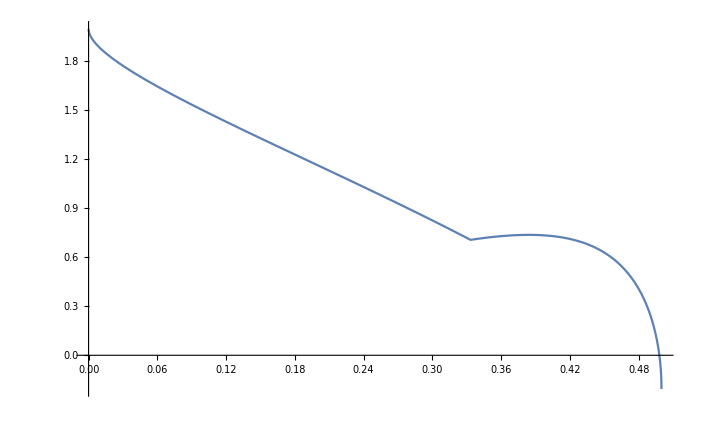

```mathematica
Plot[f0409[k],{k,0,1/2}]
```

```mathematica
NSolve[{f0409[k]==0,Element[k,Interval[{0,1/2}]]},k,Reals,WorkingPrecision->20]
```

{{k→{0.4981273862319838652}}}

```mathematica
Sqrt[k]/.{k->0.49812738623198386519672553496313851373`20.}
```

0.705781401166100342

```mathematica
Sqrt[1/k]/.{k->0.49812738623198386519672553496313851373`20.}
```

1.4168693002504574708

```mathematica
mm[[4,13]]=fullRotMat[t,4,13];
```

```mathematica
mm2[[4,13]]=fullRotMat2[x,4,13];mm2[[4,13]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | ((((((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11]) √(1-x[4,12])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12]) √x[4,12]) √(1-x[4,13])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]) √x[4,13] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √x[4,5] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12]) √(1-x[4,12])-(((((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11]) √x[4,12] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]) √(1-x[4,13])-((((((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11]) √(1-x[4,12])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12]) √x[4,12]) √x[4,13]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √(1-x[1,13]) | ((((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √(1-x[2,13])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √x[2,13] | ((((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √(1-x[3,13])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √x[3,13] | ((((((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11]) √(1-x[4,12])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12]) √x[4,12]) √(1-x[4,13])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]) √x[4,13] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √x[4,5] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √(1-x[3,12])-(((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √x[3,12]) √(1-x[4,12])-(((((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11]) √x[4,12] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √(1-x[1,12]) √x[1,13] √(1-x[2,13])-((((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √(1-x[2,12])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √x[2,12]) √x[2,13]) √(1-x[3,13])-((((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11]) √(1-x[3,12])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11]) √x[2,12]) √x[3,12]) √x[3,13]) √(1-x[4,13])-((((((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11]) √(1-x[4,12])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) √x[1,12] √(1-x[2,12])-(((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1

```mathematica
mmzero[[4,13]]=mm2[[4,13]][[;;,1;;4]]/.{x[1,13]->0,x[1,12]->0,x[1,11]->0,x[1,10]->0,x[1,9]->0,x[1,8]->0,x[2,13]->0,x[2,12]->0,x[2,11]->0,x[4,13]->0,x[4,12]->0,x[4,11]->0,x[4,10]->0,x[4,9]->0,x[4,8]->0,x[4,7]->0,x[4,6]->0,x[4,5]->0,x[3,10]->0,x[3,9]->0,x[3,8]->0,x[3,7]->0,x[3,6]->0,x[3,5]->0,x[3,4]->0,x[2,7]->0,x[2,6]->0,x[2,5]->0,x[2,3]->1,x[2,4]->0};mmzero[[4,13]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | -√(1-x[1,2]) √x[1,3] √(1-x[2,8]) √(1-x[2,9]) √(1-x[2,10]) | √x[1,2] √(1-x[3,11]) √(1-x[3,12]) √(1-x[3,13]) | -√(1-x[1,2]) √(1-x[1,3]) √x[1,4]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | -√x[1,2] √x[1,3] √(1-x[2,8]) √(1-x[2,9]) √(1-x[2,10]) | -√(1-x[1,2]) √(1-x[3,11]) √(1-x[3,12]) √(1-x[3,13]) | -√x[1,2] √(1-x[1,3]) √x[1,4]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | √(1-x[1,3]) √(1-x[2,8]) √(1-x[2,9]) √(1-x[2,10]) | 0 | -√x[1,3] √x[1,4]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | 0 | 0 | √(1-x[1,4])
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) | 0 | 0 | 0
√x[1,6] √(1-x[1,7]) | 0 | 0 | 0
√x[1,7] | 0 | 0 | 0
0 | √x[2,8] √(1-x[2,9]) √(1-x[2,10]) | 0 | 0
0 | √x[2,9] √(1-x[2,10]) | 0 | 0
0 | √x[2,10] | 0 | 0
0 | 0 | √x[3,11] √(1-x[3,12]) √(1-x[3,13]) | 0
0 | 0 | √x[3,12] √(1-x[3,13]) | 0
0 | 0 | √x[3,13] | 0)

```mathematica
mmzero00401301=FullSimplify[mmzero[[4,13]]/.{x[3,13]->k,x[2,10]->k,x[1,7]->k},Assumptions->{0<=k<=1,Reals}];mmzero00401301//MatrixForm
```

(√((-1+k) (-1+x[1,2])) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) | -√((-1+k) (-1+x[1,2])) √x[1,3] √(1-x[2,8]) √(1-x[2,9]) | √(-((-1+k) x[1,2])) √(1-x[3,11]) √(1-x[3,12]) | -√(1-x[1,2]) √(1-x[1,3]) √x[1,4]
√(-((-1+k) x[1,2])) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) | -√(-((-1+k) x[1,2])) √x[1,3] √(1-x[2,8]) √(1-x[2,9]) | -√((-1+k) (-1+x[1,2])) √(1-x[3,11]) √(1-x[3,12]) | -√x[1,2] √(1-x[1,3]) √x[1,4]
√(-((-1+k) x[1,3])) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) | √((-1+k) (-1+x[1,3])) √(1-x[2,8]) √(1-x[2,9]) | 0 | -√x[1,3] √x[1,4]
√(-((-1+k) x[1,4])) √(1-x[1,5]) √(1-x[1,6]) | 0 | 0 | √(1-x[1,4])
√(-((-1+k) x[1,5])) √(1-x[1,6]) | 0 | 0 | 0
√(-((-1+k) x[1,6])) | 0 | 0 | 0
√k | 0 | 0 | 0
0 | √(-((-1+k) x[2,8])) √(1-x[2,9]) | 0 | 0
0 | √(-((-1+k) x[2,9])) | 0 | 0
0 | √k | 0 | 0
0 | 0 | √(-((-1+k) x[3,11])) √(1-x[3,12]) | 0
0 | 0 | √(-((-1+k) x[3,12])) | 0
0 | 0 | √k | 0)

```mathematica
FullSimplify[Solve[{mmzero00401301[[6,1]]==Sqrt[k],0<=k<=1,0<=x[1,6]<=1},x[1,6],Reals],Assumptions->{0<=k<=1,0<=x[1,6]<=1,Reals}]
```

{{x[1,6]→ConditionalExpression[-k/(-1+k), 0<k<1/2]}}

```mathematica
mmzero00401302=FullSimplify[mmzero[[4,13]]/.{x[3,13]->k,x[2,10]->k,x[1,7]->k,x[1,6]->-k/(-1+k),x[2,9]->-k/(-1+k),x[3,12]->-k/(-1+k)},Assumptions->{1/2<=k<=1,Reals}];mmzero00401302//MatrixForm
```

(√(1-2 k) √(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) | -√(1-2 k) √(1-x[1,2]) √x[1,3] √(1-x[2,8]) | √(1-2 k) √x[1,2] √(1-x[3,11]) | -√(1-x[1,2]) √(1-x[1,3]) √x[1,4]
√(1-2 k) √x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) | -√(1-2 k) √x[1,2] √x[1,3] √(1-x[2,8]) | -√(1-2 k) √(1-x[1,2]) √(1-x[3,11]) | -√x[1,2] √(1-x[1,3]) √x[1,4]
√(1-2 k) √x[1,3] √(1-x[1,4]) √(1-x[1,5]) | √(1-2 k) √(1-x[1,3]) √(1-x[2,8]) | 0 | -√x[1,3] √x[1,4]
√(1-2 k) √x[1,4] √(1-x[1,5]) | 0 | 0 | √(1-x[1,4])
√(1-2 k) √x[1,5] | 0 | 0 | 0
√k | 0 | 0 | 0
√k | 0 | 0 | 0
0 | √(1-2 k) √x[2,8] | 0 | 0
0 | √k | 0 | 0
0 | √k | 0 | 0
0 | 0 | √(1-2 k) √x[3,11] | 0
0 | 0 | √k | 0
0 | 0 | √k | 0)

```mathematica
FullSimplify[Solve[{mmzero00401302[[5,1]]==Sqrt[k],0<=k<=1,0<=x[1,5]<=1},x[1,5],Reals],Assumptions->{0<=k<=1,0<=x[1,5]<=1,Reals}]
```

{{x[1,5]→ConditionalExpression[k/(1-2 k), 0<k<1/3]}}

```mathematica
mmzero00401303=FullSimplify[mmzero[[4,13]]/.{x[3,13]->k,x[2,10]->k,x[1,7]->k,x[1,6]->-k/(-1+k),x[2,9]->-k/(-1+k),x[3,12]->-k/(-1+k),x[1,5]->k/(1-2k),x[2,8]->k/(1-2k),x[3,11]->k/(1-2k)},Assumptions->{1/2<=k<=1,Reals}];mmzero00401303//MatrixForm
```

(√(1-3 k) √(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) | -√(1-3 k) √(1-x[1,2]) √x[1,3] | √(1-3 k) √x[1,2] | -√(1-x[1,2]) √(1-x[1,3]) √x[1,4]
√(1-3 k) √x[1,2] √(1-x[1,3]) √(1-x[1,4]) | -√(1-3 k) √x[1,2] √x[1,3] | -√(1-3 k) √(1-x[1,2]) | -√x[1,2] √(1-x[1,3]) √x[1,4]
√(1-3 k) √x[1,3] √(1-x[1,4]) | √(1-3 k) √(1-x[1,3]) | 0 | -√x[1,3] √x[1,4]
√(1-3 k) √x[1,4] | 0 | 0 | √(1-x[1,4])
-√k | 0 | 0 | 0
√k | 0 | 0 | 0
√k | 0 | 0 | 0
0 | -√k | 0 | 0
0 | √k | 0 | 0
0 | √k | 0 | 0
0 | 0 | -√k | 0
0 | 0 | √k | 0
0 | 0 | √k | 0)

```mathematica
FullSimplify[Solve[{mmzero00401303[[4,1]]+mmzero00401303[[4,4]]==Sqrt[k],0<=k<=1,0<=x[1,4]<=1},x[1,4],Reals],Assumptions->{0<=k<=1,0<=x[1,4]<=1,Reals}]
```

{{x[1,4]→ConditionalExpression[(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2, 1/4<k<1/3]}}

```mathematica
mmzero00401304=FullSimplify[mmzero[[4,13]]/.{x[3,13]->k,x[2,10]->k,x[1,7]->k,x[1,6]->-k/(-1+k),x[2,9]->-k/(-1+k),x[3,12]->-k/(-1+k),x[1,5]->k/(1-2k),x[2,8]->k/(1-2k),x[3,11]->k/(1-2k),x[1,4]->(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2},Assumptions->{1/2<=k<=1,Reals}];mmzero00401304//MatrixForm
```

(√(((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k)))))/(2-3 k)^2) √(1-x[1,2]) √(1-x[1,3]) | -√(1-3 k) √(1-x[1,2]) √x[1,3] | √(1-3 k) √x[1,2] | -√((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) √(1-x[1,2]) √(1-x[1,3])
√(((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k)))))/(2-3 k)^2) √x[1,2] √(1-x[1,3]) | -√(1-3 k) √x[1,2] √x[1,3] | -√(1-3 k) √(1-x[1,2]) | -√((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) √x[1,2] √(1-x[1,3])
√(((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k)))))/(2-3 k)^2) √x[1,3] | √(1-3 k) √(1-x[1,3]) | 0 | -√((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) √x[1,3]
√(1-3 k) √((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) | 0 | 0 | √((2+3 k (-3+4 k)-2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2)
-√k | 0 | 0 | 0
√k | 0 | 0 | 0
√k | 0 | 0 | 0
0 | -√k | 0 | 0
0 | √k | 0 | 0
0 | √k | 0 | 0
0 | 0 | -√k | 0
0 | 0 | √k | 0
0 | 0 | √k | 0)

```mathematica
mmzero00401304/.{k->0.5761860^2,x[1,2]->1/2,x[1,3]->0.35}//MatrixForm
Total[Map[Abs,mmzero00401304/.{k->0.5761860^2,x[1,2]->1/2,x[1,3]->0.351149}],{2}]//MatrixForm
```

(0.018891 | -0.0265535 | 0.0448836 | -0.486237
0.018891 | -0.0265535 | -0.0448836 | -0.486237
0.0196041 | 0.0511752 | 0 | -0.504592
0.0541389 | 0 | 0 | 0.522047
-0.576186 | 0 | 0 | 0
0.576186 | 0 | 0 | 0
0.576186 | 0 | 0 | 0
0 | -0.576186 | 0 | 0
0 | 0.576186 | 0 | 0
0 | 0.576186 | 0 | 0
0 | 0 | -0.576186 | 0
0 | 0 | 0.576186 | 0
0 | 0 | 0.576186 | 0)

(0.576162
0.576162
0.576186
0.576186
0.576186
0.576186
0.576186
0.576186
0.576186
0.576186
0.576186
0.576186
0.576186)

```mathematica
mmzero00401305=FullSimplify[mmzero[[4,13]]/.{x[3,13]->k,x[2,10]->k,x[1,7]->k,x[1,6]->-k/(-1+k),x[2,9]->-k/(-1+k),x[3,12]->-k/(-1+k),x[1,5]->k/(1-2k),x[2,8]->k/(1-2k),x[3,11]->k/(1-2k),x[1,4]->(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2,x[1,2]->1/2},Assumptions->{1/2<=k<=1,Reals}];mmzero00401305//MatrixForm
```

((√(((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k)))))/(2-3 k)^2) √(1-x[1,3]))/(√2) | -(√(1-3 k) √x[1,3])/(√2) | (√(1-3 k))/(√2) | -(√((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) √(1-x[1,3]))/(√2)
(√(((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k)))))/(2-3 k)^2) √(1-x[1,3]))/(√2) | -(√(1-3 k) √x[1,3])/(√2) | -(√(1-3 k))/(√2) | -(√((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) √(1-x[1,3]))/(√2)
√(((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k)))))/(2-3 k)^2) √x[1,3] | √(1-3 k) √(1-x[1,3]) | 0 | -√((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) √x[1,3]
√(1-3 k) √((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2) | 0 | 0 | √((2+3 k (-3+4 k)-2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2)
-√k | 0 | 0 | 0
√k | 0 | 0 | 0
√k | 0 | 0 | 0
0 | -√k | 0 | 0
0 | √k | 0 | 0
0 | √k | 0 | 0
0 | 0 | -√k | 0
0 | 0 | √k | 0
0 | 0 | √k | 0)

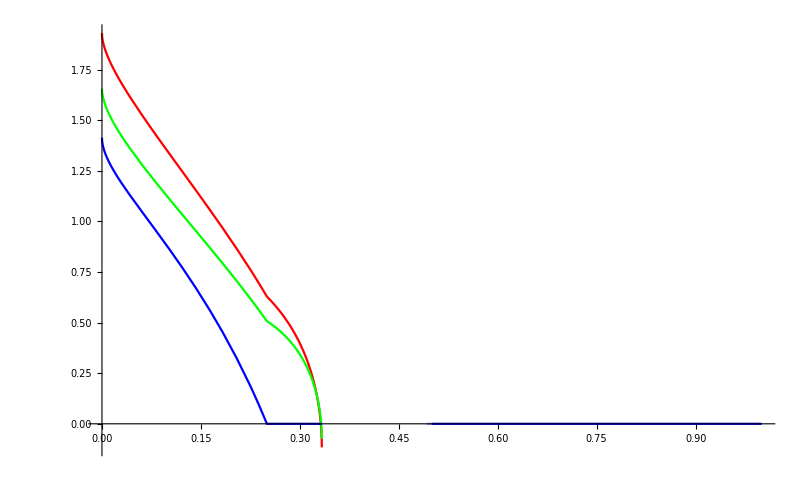

```mathematica
Plot[{(mmzero00401305[[2,1]]-mmzero00401305[[2,2]]-mmzero00401305[[2,3]]-mmzero00401305[[2,4]]-Sqrt[k])/.{x[1,3]->3/8},(mmzero00401305[[3,1]]+mmzero00401305[[3,2]]-mmzero00401305[[3,4]]-Sqrt[k])/.{x[1,3]->3/8},mmzero00401305[[4,1]]+mmzero00401305[[4,4]]-Sqrt[k]},{k,0,1},PlotStyle->{Red,Green,Blue,Purple}]
```

```mathematica
FullSimplify[(mmzero00401305/.{x[1,3]->3/8,k->0.576185648450293075306660739^2}),Assumptions->{0<=k<=1,Reals}]//MatrixForm
FullSimplify[Total[Map[Abs,N[mmzero00401305/.{x[1,3]->0.35112950000000,k->0.576185648450293075306660739^2},20]],{2}]]//MatrixForm
```

(0.0185266015660846421831856 | -0.0274896420029862443692457 | 0.044890397412730949662397 | -0.4767979438403906200677885
0.0185266015660846421831856 | -0.0274896420029862443692457 | -0.044890397412730949662397 | -0.4767979438403906200677885
0.0202948751833101920074185 | 0.0501889900759235433757404 | 0 | -0.5223059784269266289929386
0.054147425329952700775623 | 0 | 0 | 0.522038223120340374531038
-0.57618564845029307530666074 | 0 | 0 | 0
0.57618564845029307530666074 | 0 | 0 | 0
0.57618564845029307530666074 | 0 | 0 | 0
0 | -0.57618564845029307530666074 | 0 | 0
0 | 0.57618564845029307530666074 | 0 | 0
0 | 0.57618564845029307530666074 | 0 | 0
0 | 0 | -0.57618564845029307530666074 | 0
0 | 0 | 0.57618564845029307530666074 | 0
0 | 0 | 0.57618564845029307530666074 | 0)

(0.576186
0.576186
0.576186
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531
0.57618564845029307531)

```mathematica
Solve[fbb3^2 x^2+(2fbb2 fbb3-4fbb1^2)x+fbb2^2==0,x]
```

{{x→(2 fbb1^2-fbb2 fbb3-2 √(fbb1^4-fbb1^2 fbb2 fbb3))/fbb3^2},{x→(2 fbb1^2-fbb2 fbb3+2 √(fbb1^4-fbb1^2 fbb2 fbb3))/fbb3^2}}

```mathematica
FullSimplify[{{x->(2 fbb1^2-fbb2 fbb3-2 √(fbb1^4-fbb1^2 fbb2 fbb3))/fbb3^2},{x->(2 fbb1^2-fbb2 fbb3+2 √(fbb1^4-fbb1^2 fbb2 fbb3))/fbb3^2}}/.{fbb1->2fb1 fb3,fbb2->fb3^2-fb2^2,fbb3->fb2^2+fb1^2}]
```

{{x→(fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+7 fb3^2)-4 √(fb1^2 fb3^2 (fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+3 fb3^2))))/((fb1^2+fb2^2)^2)},{x→(fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+7 fb3^2)+4 √(fb1^2 fb3^2 (fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+3 fb3^2))))/((fb1^2+fb2^2)^2)}}

```mathematica
FullSimplify[{{x->(fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+7 fb3^2)-4 √(fb1^2 fb3^2 (fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+3 fb3^2))))/((fb1^2+fb2^2)^2)},{x->(fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+7 fb3^2)+4 √(fb1^2 fb3^2 (fb2^4-fb2^2 fb3^2+fb1^2 (fb2^2+3 fb3^2))))/((fb1^2+fb2^2)^2)}}/.{fb1->f1+f3,fb2->f2,fb3->f4}]
```

{{x→(f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+7 f4^2)-4 √((f1+f3)^2 f4^2 (f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+3 f4^2))))/((f2^2+(f1+f3)^2)^2)},{x→(f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+7 f4^2)+4 √((f1+f3)^2 f4^2 (f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+3 f4^2))))/((f2^2+(f1+f3)^2)^2)}}

```mathematica
FullSimplify[ExpandAll[{{x->(f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+7 f4^2)-4 √((f1+f3)^2 f4^2 (f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+3 f4^2))))/((f2^2+(f1+f3)^2)^2)},{x->(f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+7 f4^2)+4 √((f1+f3)^2 f4^2 (f2^4-f2^2 f4^2+(f1+f3)^2 (f2^2+3 f4^2))))/((f2^2+(f1+f3)^2)^2)}}/.{f1->√(((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k)))))/(2-3 k)^2),f2->√(1-3 k) ,f3->√((2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))/(2-3 k)^2),f4->Sqrt[k]}],Assumptions->{0<=k<=1,Reals}]
```

{{x→((2-3 k)^2 (8+2 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+k (-42+6 √2 √(k (1+k (-5+6 k)))+8 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+3 k (35-3 k (11+4 k)+8 √2 √(k (1+k (-5+6 k)))))-4 √2 √(k (-8100 k^5+6318 k^6-1944 k^7-96 k^(5/2) √(2+2 k (-5+6 k))+459 k^(7/2) √(2+2 k (-5+6 k))-837 k^(9/2) √(2+2 k (-5+6 k))+324 k^(11/2) √(2+2 k (-5+6 k))+12 k^(3/2) √(2+2 k (-5+6 k)) (1+√((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+12 (2+√((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+27 k^4 (249+4 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))-4 k (69+19 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))-3 k^3 (1285+93 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+k^2 (1382+213 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))))))/(80+12033 k^4-9342 k^5+3969 k^6-240 k^(5/2) √(2+2 k (-5+6 k))+612 k^(7/2) √(2+2 k (-5+6 k))-756 k^(9/2) √(2+2 k (-5+6 k))+32 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+24 k^(3/2) √(2+2 k (-5+6 k)) √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+8 k (-106+6 √2 √(k (1+k (-5+6 k)))-21 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))-84 k^3 (107+3 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+4 k^2 (946+81 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))))},{x→((2-3 k)^2 (8+2 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+k (-42+6 √2 √(k (1+k (-5+6 k)))+8 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+3 k (35-3 k (11+4 k)+8 √2 √(k (1+k (-5+6 k)))))+4 √2 √(k (-8100 k^5+6318 k^6-1944 k^7-96 k^(5/2) √(2+2 k (-5+6 k))+459 k^(7/2) √(2+2 k (-5+6 k))-837 k^(9/2) √(2+2 k (-5+6 k))+324 k^(11/2) √(2+2 k (-5+6 k))+12 k^(3/2) √(2+2 k (-5+6 k)) (1+√((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+12 (2+√((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+27 k^4 (249+4 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))-4 k (69+19 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))-3 k^3 (1285+93 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+k^2 (1382+213 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))))))/(80+12033 k^4-9342 k^5+3969 k^6-240 k^(5/2) √(2+2 k (-5+6 k))+612 k^(7/2) √(2+2 k (-5+6 k))-756 k^(9/2) √(2+2 k (-5+6 k))+32 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+24 k^(3/2) √(2+2 k (-5+6 k)) √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))+8 k (-106+6 √2 √(k (1+k (-5+6 k)))-21 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))-84 k^3 (107+3 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k)))))+4 k^2 (946+81 √((-1+3 k) (-2+3 (3-4 k) k+2 √2 √(k (1+k (-5+6 k))))) √(2-3 k (1+k)+2 √2 √(k (1+k (-5+6 k))))))}}

```mathematica
mm[[4,7]]=fullRotMat[t,4,7];
```

```mathematica
mm2[[4,7]]=fullRotMat2[x,4,7];mm2[[4,7]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | ((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | ((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | ((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √x[4,5] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | ((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | ((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | ((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √x[4,5] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | (((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | (((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | ((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7] | ((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √x[4,5] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) | ((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7] | ((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | ((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7] | ((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √(1-x[4,5])-√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √x[4,5] | ((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7]
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) | (√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7] | (√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7] | (√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7] | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √(1-x[4,5]) | ((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √(1-x[4,6])-√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √x[4,6] | ((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-(√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √x[4,7]
√x[1,6] √(1-x[1,7]) | √(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7] | √(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7] | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7] | 0 | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √(1-x[4,6]) | ((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √(1-x[4,7])-√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √x[4,7]
√x[1,7] | √(1-x[1,7]) √x[2,7] | √(1-x[1,7]) √(1-x[2,7]) √x[3,7] | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] | 0 | 0 | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √(1-x[4,7]))

```mathematica
mmzero[[4,7]]=mm2[[4,7]][[;;,1;;4]]/.{x[1,7]->0,x[1,6]->0,x[1,5]->0,x[1,4]->0,x[1,3]->0,x[2,7]->0,x[2,6]->0,x[2,5]->0,x[2,3]->1,x[3,7]->0,x[3,5]->1,x[3,4]->0};mmzero[[4,7]]//MatrixForm
```

(√(1-x[1,2]) | 0 | 0 | -√x[1,2] √x[4,5] √(1-x[4,6]) √(1-x[4,7])
√x[1,2] | 0 | 0 | √(1-x[1,2]) √x[4,5] √(1-x[4,6]) √(1-x[4,7])
0 | √(1-x[2,4]) | 0 | -√x[2,4] √(1-x[4,5]) √(1-x[4,6]) √(1-x[4,7])
0 | √x[2,4] | 0 | √(1-x[2,4]) √(1-x[4,5]) √(1-x[4,6]) √(1-x[4,7])
0 | 0 | √(1-x[3,6]) | -√x[3,6] √x[4,6] √(1-x[4,7])
0 | 0 | √x[3,6] | √(1-x[3,6]) √x[4,6] √(1-x[4,7])
0 | 0 | 0 | √x[4,7])

```mathematica
mmzero00400701=FullSimplify[mmzero[[4,7]]/.{x[4,7]->k},Assumptions->{0<=k<=1,Reals}];mmzero00400701//MatrixForm
```

(√(1-x[1,2]) | 0 | 0 | -√(-((-1+k) x[1,2])) √x[4,5] √(1-x[4,6])
√x[1,2] | 0 | 0 | √((-1+k) (-1+x[1,2])) √x[4,5] √(1-x[4,6])
0 | √(1-x[2,4]) | 0 | -√(-((-1+k) x[2,4])) √(1-x[4,5]) √(1-x[4,6])
0 | √x[2,4] | 0 | √((-1+k) (-1+x[2,4])) √(1-x[4,5]) √(1-x[4,6])
0 | 0 | √(1-x[3,6]) | -√(-((-1+k) x[3,6])) √x[4,6]
0 | 0 | √x[3,6] | √((-1+k) (-1+x[3,6])) √x[4,6]
0 | 0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00400701[[6,3]]+mmzero00400701[[6,4]]==Sqrt[k],mmzero00400701[[5,3]]-mmzero00400701[[5,4]]==Sqrt[k],0<=k<=1,0<=x[3,6]<=1,0<=x[4,6]<=1},{x[3,6],x[4,6]},Reals],Assumptions->{0<=k<=1,0<=x[3,6]<=1,0<=x[4,6]<=1,Reals}]
```

{{x[3,6]→ConditionalExpression[1/2, 1/2<k<8/9],x[4,6]→ConditionalExpression[-2+(-3+2 √2 √k)/(-1+k), 1/2<k<8/9]}}

```mathematica
mmzero00400702=FullSimplify[mmzero[[4,7]]/.{x[4,7]->k,x[3,6]->1/2,x[4,6]->-2+(-3+2 √2 √k)/(-1+k)},Assumptions->{1/2<=k<=8/9,Reals}];mmzero00400702//MatrixForm
```

(√(1-x[1,2]) | 0 | 0 | -√((2 √2 √k-3 k) x[1,2]) √x[4,5]
√x[1,2] | 0 | 0 | √((-2 √2 √k+3 k) (-1+x[1,2])) √x[4,5]
0 | √(1-x[2,4]) | 0 | -√((2 √2 √k-3 k) x[2,4]) √(1-x[4,5])
0 | √x[2,4] | 0 | √((-2 √2 √k+3 k) (-1+x[2,4])) √(1-x[4,5])
0 | 0 | 1/(√2) | 1/(√2)-√k
0 | 0 | 1/(√2) | -1/(√2)+√k
0 | 0 | 0 | √k)

```mathematica
mmzero00400703=FullSimplify[mmzero[[4,7]]/.{x[4,7]->k,x[3,6]->1/2,x[4,6]->-2+(-3+2 √2 √k)/(-1+k),x[2,4]->1/2,x[1,2]->1/2},Assumptions->{1/2<=k<=8/9,Reals}];mmzero00400703//MatrixForm
```

(1/(√2) | 0 | 0 | -√(√2 √k x[4,5]-3/2 k x[4,5])
1/(√2) | 0 | 0 | √(√2 √k x[4,5]-3/2 k x[4,5])
0 | 1/(√2) | 0 | -(√((-2 √2+3 √k) √k (-1+x[4,5])))/(√2)
0 | 1/(√2) | 0 | √(-√2 √k (-1+x[4,5])+3/2 k (-1+x[4,5]))
0 | 0 | 1/(√2) | 1/(√2)-√k
0 | 0 | 1/(√2) | -1/(√2)+√k
0 | 0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00400703[[4,2]]+mmzero00400703[[4,4]]==Sqrt[k],1/2<=k<=8/9,0<=x[4,5]<=1},x[4,5],Reals],Assumptions->{1/2<=k<=8/9,0<=x[4,5]<=1,Reals}]
```

{{x[4,5]→ConditionalExpression[(13-(2 √2)/(√k)+2 √2 √k-15 k)/(8-9 k), 1/2<k<1/25 (11+4 √6)]}}

```mathematica
mmzero00400704=FullSimplify[mmzero[[4,7]]/.{x[4,7]->k,x[3,6]->1/2,x[4,6]->-2+(-3+2 √2 √k)/(-1+k),x[2,4]->1/2,x[1,2]->1/2,x[4,5]->(13-(2 √2)/(√k)+2 √2 √k-15 k)/(8-9 k)},Assumptions->{1/2<=k<=1/25 (11+4 √6),Reals}];mmzero00400704//MatrixForm
```

(1/(√2) | 0 | 0 | -(√(-1+4 √2 √k-5 k))/(√2)
1/(√2) | 0 | 0 | (√(-1+4 √2 √k-5 k))/(√2)
0 | 1/(√2) | 0 | 1/(√2)-√k
0 | 1/(√2) | 0 | -1/(√2)+√k
0 | 0 | 1/(√2) | 1/(√2)-√k
0 | 0 | 1/(√2) | -1/(√2)+√k
0 | 0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00400704[[2,1]]+mmzero00400704[[2,4]]==Sqrt[k],1/2<=k<=1/25 (11+4 √6)},k,Reals],Assumptions->{1/2<=k<=1/25 (11+4 √6),Reals}]
```

{{k→2/49 (11+6 √2)}}

```mathematica
FullSimplify[mmzero00400704/.{k->2/49 (11+6 √2)}//MatrixForm,Reals]
```

(1/(√2) | 0 | 0 | 1/14 (-4+√2)
1/(√2) | 0 | 0 | 1/14 (4-√2)
0 | 1/(√2) | 0 | 1/14 (-4+√2)
0 | 1/(√2) | 0 | 1/14 (4-√2)
0 | 0 | 1/(√2) | 1/14 (-4+√2)
0 | 0 | 1/(√2) | 1/14 (4-√2)
0 | 0 | 0 | 1/7 (2+3 √2))

```mathematica
N[FullSimplify[mmzero00400704/.{k->2/49 (11+6 √2)}//MatrixForm,Reals],20]
```

(0.7071067811865475244 | 0 | 0 | -0.18469903125906463937
0.7071067811865475244 | 0 | 0 | 0.18469903125906463937
0 | 0.7071067811865475244 | 0 | -0.18469903125906463937
0 | 0.7071067811865475244 | 0 | 0.18469903125906463937
0 | 0 | 0.7071067811865475244 | -0.18469903125906463937
0 | 0 | 0.7071067811865475244 | 0.18469903125906463937
0 | 0 | 0 | 0.89180581244561216377)

```mathematica
N[k/.{k->2/49 (11+6 √2)},20]
```

0.7953176071117783793

```mathematica
N[Sqrt[k]/.{k->2/49 (11+6 √2)},20]
```

0.89180581244561216377

```mathematica
FullSimplify[(1/k)/.{k->2/49 (11+6 √2)}]
```

11/2-3 √2

```mathematica
N[FullSimplify[(1/k)/.{k->2/49 (11+6 √2)}],20]
```

1.2573593128807148536

```mathematica
FullSimplify[Sqrt[(1/k)]/.{k->2/49 (11+6 √2)}]
```

-1+3/(√2)

```mathematica
N[FullSimplify[Sqrt[(1/k)]/.{k->2/49 (11+6 √2)}],20]
```

1.1213203435596425732

```mathematica
Expand[(l-Sqrt[11/2-3 √2])(l+Sqrt[11/2-3 √2])(l-Sqrt[11/2+3 √2])(l+Sqrt[11/2+3 √2])]
```

49/4-11 l^2+l^4

```mathematica
mm[[4,11]]=fullRotMat[t,4,11];
```

```mathematica
mm2[[4,11]]=fullRotMat2[x,4,11];mm2[[4,11]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | ((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | ((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | ((((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √x[4,5] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((((((((-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]) √(1-x[3,4])+(-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((-√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3]) √(1-x[2,4])-√(1-x[1,2]) √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√(1-x[1,2]) √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | ((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | ((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | ((((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √x[4,5] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((((((((-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √(1-x[3,4])-(-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((((-√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]) √(1-x[3,4])+(-√x[1,2] √(1-x[1,3]) √x[1,4] √(1-x[2,4])-(√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √(1-x[2,5])-((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((((√(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3]) √(1-x[2,4])-√x[1,2] √(1-x[1,3]) √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,2] √(1-x[1,3]) √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | (((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | (((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | ((((((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | ((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √(1-x[4,5])-((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √x[4,5] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(((((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((((((((-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √(1-x[3,4])-√(1-x[1,3]) √(1-x[2,3]) √x[3,4]) √(1-x[4,5])+((-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √(1-x[3,5])-(√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((((√(1-x[1,3]) √(1-x[2,3]) √(1-x[3,4])+(-√x[1,3] √x[1,4] √(1-x[2,4])-√(1-x[1,3]) √x[2,3] √x[2,4]) √x[3,4]) √(1-x[3,5])+(-√x[1,3] √(1-x[1,4]) √x[1,5] √(1-x[2,5])-(√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √(1-x[2,6])-((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((((√(1-x[1,3]) √x[2,3] √(1-x[2,4])-√x[1,3] √x[1,4] √x[2,4]) √(1-x[2,5])-√x[1,3] √(1-x[1,4]) √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,3] √(1-x[1,4]) √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | ((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | ((((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | ((((((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | ((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √(1-x[4,5])-√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √x[4,5] | ((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √(1-x[4,6])-(√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √x[4,6] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(((((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((((((√(1-x[1,4]) √(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])+((-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √(1-x[3,5])-√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √x[3,5]) √x[4,5]) √(1-x[4,6])+((-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √(1-x[3,6])-(√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((((√(1-x[1,4]) √(1-x[2,4]) √x[3,4] √(1-x[3,5])+(-√x[1,4] √x[1,5] √(1-x[2,5])-√(1-x[1,4]) √x[2,4] √x[2,5]) √x[3,5]) √(1-x[3,6])+(-√x[1,4] √(1-x[1,5]) √x[1,6] √(1-x[2,6])-(√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √(1-x[2,7])-((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((((√(1-x[1,4]) √x[2,4] √(1-x[2,5])-√x[1,4] √x[1,5] √x[2,5]) √(1-x[2,6])-√x[1,4] √(1-x[1,5]) √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,4] √(1-x[1,5]) √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | (((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | (((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | (((((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | √(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √(1-x[4,5]) | ((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √(1-x[4,6])-√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √x[4,6] | ((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √(1-x[4,7])-(√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √x[4,7] | ((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-(((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-((((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-(((((√(1-x[1,5]) √(1-x[2,5]) √(1-x[3,5]) √x[4,5] √(1-x[4,6])+((-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √(1-x[3,6])-√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √x[3,6]) √x[4,6]) √(1-x[4,7])+((-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √(1-x[3,7])-(√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((((√(1-x[1,5]) √(1-x[2,5]) √x[3,5] √(1-x[3,6])+(-√x[1,5] √x[1,6] √(1-x[2,6])-√(1-x[1,5]) √x[2,5] √x[2,6]) √x[3,6]) √(1-x[3,7])+(-√x[1,5] √(1-x[1,6]) √x[1,7] √(1-x[2,7])-(√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √(1-x[2,8])-((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(((√(1-x[1,5]) √x[2,5] √(1-x[2,6])-√x[1,5] √x[1,6] √x[2,6]) √(1-x[2,7])-√x[1,5] √(1-x[1,6]) √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,5] √(1-x[1,6]) √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | ((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | ((((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | ((((√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | 0 | √(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √(1-x[4,6]) | ((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √(1-x[4,7])-√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √x[4,7] | ((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √(1-x[4,8])-(√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √x[4,8] | ((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-((√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √x[4,9] | ((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(((√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((((√(1-x[1,6]) √(1-x[2,6]) √(1-x[3,6]) √x[4,6] √(1-x[4,7])+((-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √(1-x[3,7])-√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √x[3,7]) √x[4,7]) √(1-x[4,8])+((-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √(1-x[3,8])-(√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(((√(1-x[1,6]) √(1-x[2,6]) √x[3,6] √(1-x[3,7])+(-√x[1,6] √x[1,7] √(1-x[2,7])-√(1-x[1,6]) √x[2,6] √x[2,7]) √x[3,7]) √(1-x[3,8])+(-√x[1,6] √(1-x[1,7]) √x[1,8] √(1-x[2,8])-(√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,6] √(1-x[1,7]) √(1-x[1,8]) √x[1,9] √(1-x[2,9])-((√(1-x[1,6]) √x[2,6] √(1-x[2,7])-√x[1,6] √x[1,7] √x[2,7]) √(1-x[2,8])-√x[1,6] √(1-x[1,7]) √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | (((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | (((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | (((√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √(1-x[4,8])+((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | 0 | 0 | √(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √(1-x[4,7]) | ((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √(1-x[4,8])-√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √x[4,8] | ((-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9]) √(1-x[4,9])-(√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √(1-x[4,8])+((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √x[4,8]) √x[4,9] | ((-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-((√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √(1-x[4,8])+((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-(((√(1-x[1,7]) √(1-x[2,7]) √(1-x[3,7]) √x[4,7] √(1-x[4,8])+((-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √(1-x[3,8])-√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √x[3,8]) √x[4,8]) √(1-x[4,9])+((-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √(1-x[3,9])-(√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,7] √(1-x[1,8]) √(1-x[1,9]) √x[1,10] √(1-x[2,10])-((√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √(1-x[2,9])-√x[1,7] √(1-x[1,8]) √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-((√(1-x[1,7]) √(1-x[2,7]) √x[3,7] √(1-x[3,8])+(-√x[1,7] √x[1,8] √(1-x[2,8])-√(1-x[1,7]) √x[2,7] √x[2,8]) √x[3,8]) √(1-x[3,9])+(-√x[1,7] √(1-x[1,8]) √x[1,9] √(1-x[2,9])-(√(1-x[1,7]) √x[2,7] √(1-x[2,8])-√x[1,7] √x[1,8] √x[2,8]) √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √(1-x[1,11]) | ((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √x[2,11] | ((√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | ((√(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √x[4,8] √(1-x[4,9])+((-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | 0 | 0 | 0 | √(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √(1-x[4,8]) | ((-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9]) √(1-x[4,9])-√(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √x[4,8] √x[4,9] | ((-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √x[3,10]) √(1-x[4,10])-(√(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √x[4,8] √(1-x[4,9])+((-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9]) √x[4,9]) √x[4,10] | ((-√x[1,8] √(1-x[1,9]) √(1-x[1,10]) √x[1,11] √(1-x[2,11])-((√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √(1-x[2,10])-√x[1,8] √(1-x[1,9]) √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-((√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √(1-x[3,10])+(-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √x[3,10]) √x[3,11]) √(1-x[4,11])-((√(1-x[1,8]) √(1-x[2,8]) √(1-x[3,8]) √x[4,8] √(1-x[4,9])+((-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √(1-x[3,9])-√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √x[3,9]) √x[4,9]) √(1-x[4,10])+((-√x[1,8] √(1-x[1,9]) √x[1,10] √(1-x[2,10])-(√(1-x[1,8]) √x[2,8] √(1-x[2,9])-√x[1,8] √x[1,9] √x[2,9]) √x[2,10]) √(1-x[3,10])-(√(1-x[1,8]) √(1-x[2,8]) √x[3,8] √(1-x[3,9])+(-√x[1,8] √x[1,9] √(1-x[2,9])-√(1-x[1,8]) √x[2,8] √x[2,9]) √x[3,9]) √x[3,10]) √x[4,10]) √x[4,11]
√x[1,9] √(1-x[1,10]) √(1-x[1,11]) | (√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √(1-x[2,11])-√x[1,9] √(1-x[1,10]) √x[1,11] √x[2,11] | (√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √(1-x[3,10])+(-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √x[3,10]) √(1-x[3,11])+(-√x[1,9] √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √x[2,11]) √x[3,11] | (√(1-x[1,9]) √(1-x[2,9]) √(1-x[3,9]) √x[4,9] √(1-x[4,10])+((-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √(1-x[3,10])-√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √x[3,10]) √x[4,10]) √(1-x[4,11])+((-√x[1,9] √(1-x[1,10]) √x[1,11] √(1-x[2,11])-(√(1-x[1,9]) √x[2,9] √(1-x[2,10])-√x[1,9] √x[1,10] √x[2,10]) √x[2,11]) √(1-x[3,11])-(√(1-x[1,9]) √(1-x[2,9]) √x[3,9] √(1-x[3,10])+(-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,9]) √x[2,9] √x[2,10]) √x[3,10]) √x[3,11]) √x[4,11] | 0 | 0 | 0 | 0 | √(1-x[1,9]) √(1-x[2,9]) √(1-x[3,9]) √(1-x[4,9]) | ((-√x[1,9] √x[1,10] √(1-x[2,10])-√(1-x[1,

```mathematica
mmzero[[4,11]]=mm2[[4,11]][[;;,1;;4]]/.{x[1,11]->0,x[1,10]->0,x[1,9]->0,x[1,7]->0,x[1,6]->0,x[1,5]->0,x[1,4]->0,x[1,3]->0,x[2,11]->0,x[2,10]->0,x[2,8]->0,x[2,7]->0,x[2,6]->0,x[3,11]->0,x[3,9]->0,x[3,8]->0,x[3,7]->0,x[4,10]->0,x[4,9]->0,x[4,8]->0,x[3,5]->1,x[2,5]->0,x[2,3]->1};mmzero[[4,11]]//MatrixForm
```

(√(1-x[1,2]) √(1-x[1,8]) | 0 | 0 | (-√x[1,2] √x[3,4] √(1-x[4,5])-√x[1,2] √(1-x[3,4]) √x[4,5]) √(1-x[4,6]) √(1-x[4,7]) √(1-x[4,11])
√x[1,2] √(1-x[1,8]) | 0 | 0 | (√(1-x[1,2]) √x[3,4] √(1-x[4,5])+√(1-x[1,2]) √(1-x[3,4]) √x[4,5]) √(1-x[4,6]) √(1-x[4,7]) √(1-x[4,11])
0 | √(1-x[2,4]) √(1-x[2,9]) | 0 | (-√x[2,4] √(1-x[3,4]) √(1-x[4,5])+√x[2,4] √x[3,4] √x[4,5]) √(1-x[4,6]) √(1-x[4,7]) √(1-x[4,11])
0 | √x[2,4] √(1-x[2,9]) | 0 | (√(1-x[2,4]) √(1-x[3,4]) √(1-x[4,5])-√(1-x[2,4]) √x[3,4] √x[4,5]) √(1-x[4,6]) √(1-x[4,7]) √(1-x[4,11])
0 | 0 | √(1-x[3,6]) √(1-x[3,10]) | -√x[3,6] √x[4,6] √(1-x[4,7]) √(1-x[4,11])
0 | 0 | √x[3,6] √(1-x[3,10]) | √(1-x[3,6]) √x[4,6] √(1-x[4,7]) √(1-x[4,11])
0 | 0 | 0 | √x[4,7] √(1-x[4,11])
√x[1,8] | 0 | 0 | 0
0 | √x[2,9] | 0 | 0
0 | 0 | √x[3,10] | 0
0 | 0 | 0 | √x[4,11])

```mathematica
mmzero00401101=FullSimplify[mmzero[[4,11]]/.{x[4,11]->k,x[3,10]->k,x[2,9]->k,x[1,8]->k},Assumptions->{0<=k<=1,Reals}];mmzero00401101//MatrixForm
```

(√((-1+k) (-1+x[1,2])) | 0 | 0 | -√x[1,2] (√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5]) √((-1+k) (-1+x[4,6])) √(1-x[4,7])
√(-((-1+k) x[1,2])) | 0 | 0 | √(1-x[1,2]) (√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5]) √((-1+k) (-1+x[4,6])) √(1-x[4,7])
0 | √((-1+k) (-1+x[2,4])) | 0 | √x[2,4] (-√(1-x[3,4]) √(1-x[4,5])+√x[3,4] √x[4,5]) √((-1+k) (-1+x[4,6])) √(1-x[4,7])
0 | √(-((-1+k) x[2,4])) | 0 | √(1-x[2,4]) (√(1-x[3,4]) √(1-x[4,5])-√x[3,4] √x[4,5]) √((-1+k) (-1+x[4,6])) √(1-x[4,7])
0 | 0 | √((-1+k) (-1+x[3,6])) | -√(-((-1+k) x[3,6])) √x[4,6] √(1-x[4,7])
0 | 0 | √(-((-1+k) x[3,6])) | √((-1+k) (-1+x[3,6])) √x[4,6] √(1-x[4,7])
0 | 0 | 0 | √(-((-1+k) x[4,7]))
√k | 0 | 0 | 0
0 | √k | 0 | 0
0 | 0 | √k | 0
0 | 0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00401101[[7,4]]==Sqrt[k],0<=k<=1,0<=x[4,7]<=1},x[4,7],Reals],Assumptions->{0<=k<=1,0<=x[4,7]<=1}]
```

{{x[4,7]→ConditionalExpression[-k/(-1+k), 0<k<1/2]}}

```mathematica
mmzero00401102=FullSimplify[mmzero[[4,11]]/.{x[4,11]->k,x[3,10]->k,x[2,9]->k,x[1,8]->k,x[4,7]->-k/(k-1)},Assumptions->{0<=k<=1/2,Reals}];mmzero00401102//MatrixForm
```

(√((-1+k) (-1+x[1,2])) | 0 | 0 | -√x[1,2] (√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5]) √((-1+2 k) (-1+x[4,6]))
√(-((-1+k) x[1,2])) | 0 | 0 | √(1-x[1,2]) (√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5]) √((-1+2 k) (-1+x[4,6]))
0 | √((-1+k) (-1+x[2,4])) | 0 | √x[2,4] (-√(1-x[3,4]) √(1-x[4,5])+√x[3,4] √x[4,5]) √((-1+2 k) (-1+x[4,6]))
0 | √(-((-1+k) x[2,4])) | 0 | √(1-x[2,4]) (√(1-x[3,4]) √(1-x[4,5])-√x[3,4] √x[4,5]) √((-1+2 k) (-1+x[4,6]))
0 | 0 | √((-1+k) (-1+x[3,6])) | -√((1-2 k) x[3,6]) √x[4,6]
0 | 0 | √(-((-1+k) x[3,6])) | √((-1+2 k) (-1+x[3,6])) √x[4,6]
0 | 0 | 0 | √k
√k | 0 | 0 | 0
0 | √k | 0 | 0
0 | 0 | √k | 0
0 | 0 | 0 | √k)

```mathematica
mmzero00401103=FullSimplify[mmzero[[4,11]]/.{x[4,11]->k,x[3,10]->k,x[2,9]->k,x[1,8]->k,x[4,7]->-k/(k-1),x[3,6]->1/2,x[2,4]->1/2,x[1,2]->1/2},Assumptions->{0<=k<=1/2,Reals}];mmzero00401103//MatrixForm
```

((√(1-k))/(√2) | 0 | 0 | -((√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5]) √((-1+2 k) (-1+x[4,6])))/(√2)
(√(1-k))/(√2) | 0 | 0 | ((√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5]) √((-1+2 k) (-1+x[4,6])))/(√2)
0 | (√(1-k))/(√2) | 0 | ((-√(1-x[3,4]) √(1-x[4,5])+√x[3,4] √x[4,5]) √((-1+2 k) (-1+x[4,6])))/(√2)
0 | (√(1-k))/(√2) | 0 | ((√(1-x[3,4]) √(1-x[4,5])-√x[3,4] √x[4,5]) √((-1+2 k) (-1+x[4,6])))/(√2)
0 | 0 | (√(1-k))/(√2) | -(√((1-2 k) x[4,6]))/(√2)
0 | 0 | (√(1-k))/(√2) | (√((1-2 k) x[4,6]))/(√2)
0 | 0 | 0 | √k
√k | 0 | 0 | 0
0 | √k | 0 | 0
0 | 0 | √k | 0
0 | 0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00401103[[6,3]]+mmzero00401103[[6,4]]==Sqrt[k],0<=k<=1,0<=x[4,6]<=1},x[4,6],Reals],Assumptions->{0<=k<=1/2,0<=x[4,6]<=1}]
```

{{x[4,6]→ConditionalExpression[(1+k-2 √2 √(-((-1+k) k)))/(1-2 k), 1/3<k<8/17]}}

```mathematica
mmzero00401104=FullSimplify[mmzero[[4,11]]/.{x[4,11]->k,x[3,10]->k,x[2,9]->k,x[1,8]->k,x[4,7]->-k/(k-1),x[3,6]->1/2,x[2,4]->1/2,x[1,2]->1/2,x[4,6]->(1+k-2 √2 √(-((-1+k) k)))/(1-2 k)},Assumptions->{1/3<=k<=8/17,Reals}];mmzero00401104//MatrixForm
```

((√(1-k))/(√2) | 0 | 0 | -√(-(3 k)/2+√2 √((1-k) k)) (√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5])
(√(1-k))/(√2) | 0 | 0 | 1/2 √(-6 k+4 √2 √((1-k) k)) (√x[3,4] √(1-x[4,5])+√(1-x[3,4]) √x[4,5])
0 | (√(1-k))/(√2) | 0 | 1/2 √(-6 k+4 √2 √((1-k) k)) (-√(1-x[3,4]) √(1-x[4,5])+√x[3,4] √x[4,5])
0 | (√(1-k))/(√2) | 0 | 1/2 √(-6 k+4 √2 √((1-k) k)) (√(1-x[3,4]) √(1-x[4,5])-√x[3,4] √x[4,5])
0 | 0 | (√(1-k))/(√2) | -(√(1+k-2 √2 √(-((-1+k) k))))/(√2)
0 | 0 | (√(1-k))/(√2) | (√(1+k-2 √2 √(-((-1+k) k))))/(√2)
0 | 0 | 0 | √k
√k | 0 | 0 | 0
0 | √k | 0 | 0
0 | 0 | √k | 0
0 | 0 | 0 | √k)

```mathematica
(mmzero00401104/.{k->0.6655790^2,x[3,4]->1,x[4,5]->1/2})//MatrixForm
```

(0.527733 | 0 | 0 | -0.137846
0.527733 | 0 | 0 | 0.137846
0 | 0.527733 | 0 | 0.137846
0 | 0.527733 | 0 | -0.137846
0 | 0 | 0.527733 | -0.137846
0 | 0 | 0.527733 | 0.137846
0 | 0 | 0 | 0.665579
0.665579 | 0 | 0 | 0
0 | 0.665579 | 0 | 0
0 | 0 | 0.665579 | 0
0 | 0 | 0 | 0.665579)

```mathematica
mmzero00401105=FullSimplify[mmzero[[4,11]]/.{x[4,11]->k,x[3,10]->k,x[2,9]->k,x[1,8]->k,x[4,7]->-k/(k-1),x[3,6]->1/2,x[2,4]->1/2,x[1,2]->1/2,x[4,6]->(1+k-2 √2 √(-((-1+k) k)))/(1-2 k),x[3,4]->1/2+Sqrt[2]/4,x[4,5]->1/2+Sqrt[2]/4},Assumptions->{1/3<=k<=8/17,Reals}];mmzero00401105//MatrixForm
```

((√(1-k))/(√2) | 0 | 0 | -1/2 √(-3 k+2 √2 √(-((-1+k) k)))
(√(1-k))/(√2) | 0 | 0 | 1/2 √(-3 k+2 √2 √(-((-1+k) k)))
0 | (√(1-k))/(√2) | 0 | 1/2 √(-3 k+2 √2 √(-((-1+k) k)))
0 | (√(1-k))/(√2) | 0 | -1/2 √(-3 k+2 √2 √(-((-1+k) k)))
0 | 0 | (√(1-k))/(√2) | -(√(1+k-2 √2 √(-((-1+k) k))))/(√2)
0 | 0 | (√(1-k))/(√2) | (√(1+k-2 √2 √(-((-1+k) k))))/(√2)
0 | 0 | 0 | √k
√k | 0 | 0 | 0
0 | √k | 0 | 0
0 | 0 | √k | 0
0 | 0 | 0 | √k)

```mathematica
FullSimplify[Solve[{mmzero00401105[[4,2]]-mmzero00401105[[4,4]]==Sqrt[k],1/3<=k<=8/17},Reals],Assumptions->{1/3<=k<=8/17,Reals}]
```

{{k→2/97 (13+6 √2)}}

```mathematica
N[k/.{k->2/97 (13+6 √2)},20]
```

0.44299549225234165552

```mathematica
FullSimplify[mmzero00401105/.{k->2/97 (13+6 √2)}//MatrixForm,Reals]
```

(√(1/194 (71-12 √2)) | 0 | 0 | Root-0.138Root[1-60 #1^2+388 #1^4&,2]-0.13784593785292615
√(1/194 (71-12 √2)) | 0 | 0 | √(1/194 (15-8 √2))
0 | √(1/194 (71-12 √2)) | 0 | √(1/194 (15-8 √2))
0 | √(1/194 (71-12 √2)) | 0 | Root-0.138Root[1-60 #1^2+388 #1^4&,2]-0.13784593785292615
0 | 0 | √(1/194 (71-12 √2)) | Root-0.138Root[1-60 #1^2+388 #1^4&,2]-0.13784593785292615
0 | 0 | √(1/194 (71-12 √2)) | √(1/194 (15-8 √2))
0 | 0 | 0 | √(2/97 (13+6 √2))
√(2/97 (13+6 √2)) | 0 | 0 | 0
0 | √(2/97 (13+6 √2)) | 0 | 0
0 | 0 | √(2/97 (13+6 √2)) | 0
0 | 0 | 0 | √(2/97 (13+6 √2)))

```mathematica
N[FullSimplify[mmzero00401105/.{k->2/97 (13+6 √2)}//MatrixForm,Reals],20]
```

(0.52773312751222011213 | 0 | 0 | -0.1378459378529261612
0.52773312751222011213 | 0 | 0 | 0.1378459378529261612
0 | 0.52773312751222011213 | 0 | 0.1378459378529261612
0 | 0.52773312751222011213 | 0 | -0.1378459378529261612
0 | 0 | 0.52773312751222011213 | -0.1378459378529261612
0 | 0 | 0.52773312751222011213 | 0.1378459378529261612
0 | 0 | 0 | 0.66557906536514627333
0.66557906536514627333 | 0 | 0 | 0
0 | 0.66557906536514627333 | 0 | 0
0 | 0 | 0.66557906536514627333 | 0
0 | 0 | 0 | 0.66557906536514627333)

```mathematica
N[Sqrt[k]/.{k->2/97 (13+6 √2)},20]
```

0.66557906536514627333

```mathematica
FullSimplify[(1/k)/.{k->2/97 (13+6 √2)}]
```

13/2-3 √2

```mathematica
N[(1/k)/.{k->2/97 (13+6 √2)},20]
```

2.2573593128807148536

```mathematica
FullSimplify[Sqrt[1/k]/.{k->2/97 (13+6 √2)}]
```

√(13/2-3 √2)

```mathematica
N[FullSimplify[Sqrt[1/k]/.{k->2/97 (13+6 √2)}],20]
```

1.5024511016604549895

```mathematica
Expand[(l-√(13/2-3 √2))(l+√(13/2-3 √2))(l-√(13/2+3 √2))(l+√(13/2+3 √2))]
```

97/4-13 l^2+l^4